# Form Factor Dependence in Guichon et al's Hartree-Fock QMC Model

## Notes on the Hartree-Fock Quark-Meson Coupling model (HF-QMC) model as it appears in Nucl. Phys. A772 (2006) 1-19 and Nucl. Phys. A792 (2007) 341-369, but with inclusion of a dipole form factor.

Notebook author: D. L. Whittenbury 
Initial Version: v1.0 January 2016
Previous Version: v1.1 updated 10 June 2016
Current Version: v1.2 6 March 2020
Comments: v1.2: Checked if worked with Mathematica 12.
Wolfram Mathematica:
	- 7 used for v1.0
	- 10 used for v1.1
	- 12 used for v1.2

Terms of use: This notebook can be freely used for private and pedagogical purposes. If use leads to publication, then appropriate acknowledgement in the form of citations is appreciated.  Note that this notebook does NOT calculate the same model variations as in my paper Phys. Rev. C89 (065801) except for the Hartree scenario. Most importantly, this is not a sophisticated numerical calculation and NO guarantee of correctness is given. Use this notebook at your own risk! Increasing the working precision can significantly affect the time taken to run the notebook. Setting WP = 16 is very slow, but some model variations require this to find a solution for nuclear matter saturation. Functions are mostly written for symmetric nuclear matter only, but could be generalised.

For bugs or any other signs of incompetence, corrections can be sent to whittenburydaniel@gmail.com. Questions and/or comments are also welcome.

## This notebook

This notebook minimally extends the above two papers calculation of Symmetric Nuclear Matter (SNM) to include a form factor. The aim was just to quickly see the EoS dependence on the various contributions and approximations. Throughout default options were mostly used and so the calculation could be improved to be more precise, which will SIGNIFICANTLY slow the notebook and should rather be done in Fortran, C or C++. However, this should still be useful for understanding how such a calculation can be done and the various contribution to the EoS.
 
This notebook has been written to examine the Hartree-Fock QMC model as it appears in the above two papers. Here we focus on SNM and in particular the simplified Fock terms and various contributions to the energy density, the incompressibility and the slope of the symmetry energy. It can calculate:

Energy Density

Binding Energy (SNM only)

Pressure (SNM only)

Incompressibility (SNM only)

Symmetry Energy (Two methods difference and numerical finite difference formulas)

Slope of the Symmetry Energy (using either method)

Fit couplings and find saturation properties

Create EoS table

Create figures and tables for a few model variations

There are examples of use throughout. Note that the calculation and figures before the section ``Actual Calculations for model variations" are only for testing the functions. These can be commented out to speed up the notebook. They use rounded off values for one set of couplings taken from the 2007 paper, the specific value for binding energy at saturation is -15.865MeV,  RNFREE = 0.8fm,  S_0=30MeV, ... and do not readjust for different variations of the model.

### Possible difference in my calculation and the above two papers

Possible differences in my calculation and the above two papers:

Free masses, i.e., the values of m_ω, m_ρ, m_π, M_N used in Guichon/Stone papers are not know (by me), so when fitting couplings the results may not be exactly the same.

Also possible differences in the numerical approximations, e.g., finite difference type, order and increment size.

It is also not clear to me how the effective sigma mass and scalar field were calculated. It appears that the mean field result for the scalar field was used. For the effective sigma mass I use the non-relativistic approximation given in Eq.~23 of the 2006 paper for simplicity.

The way the symmetry energy is calculated, i.e., difference method or numerical derivative.
To get close to the coupling values found in the above papers I must use the numerical finite difference calculation of the symmetry energy despite the fact that it is stated in the second paper they use the difference method. This is unusual !

### A few comments on using this notebook

Comments on using this notebook:

You must set your path to this notebook below, otherwise you will have errors. If you do not set the path correctly mathematica will not know where to put the calculated data files this notebook creates and also where to find the HIC data file used in the pressure versus density plots. Note that the data files that are written to disk may have many columns which may flow over onto the next line, keep this in mind when inspecting them in a text editor.

First run the notebook without the Fock contribution to the scalar field in the function  ``FSigma[... ]" (it is commented out already). It will be much faster without this contribution and there will be no complaints about not knowing about ``DϵFσDσ". The first few sections just use the couplings given in Guichon et al's paper. These calculations are just for testing purposes and can be commented out. 

If you want the Fock correction to the scalar field, once run uncomment ``DϵFσDσ" in FSigma and recalculate the latter sections. This will include the Fock correction to the scalar field. In the papers by Guichon, it looks as if he doesn’t include this. BUT DO NOT USE THE OPTION ``Effρs" THIS WILL GIVE A RECURSION ERROR !

For the Fock terms use ∞ for the cut-off if you don't want the form factor. It will evaluate the Fock terms faster as the angular integral has been done analytically and the resulting equations programmed. If you use 0 for a cut-off then no Fock contribution for that meson will be included. If you use a finite value in GeV the form factor will be included with that cut-off value.

Throughout we use this option in NIntegrate 
Method → {Automatic, "SymbolicProcessing" → 0}" 
it tells NIntegrate not to try and evaluate the integral symbolically rather just do it numerically. This is usually much faster.

### Data from the above two papers

Data from papers: A: 2006 B:2007

An asterisk indicates a quantity used in constraining the model parameters.

```mathematica
TableOneHeadings = {"Model","B. En.^*","S_0^*","ρ_0^*","G_σ","G_ω","G_ρ","K_0","L_0"};
TableOneUnits = {"", "[MeV]","[MeV]","[fm^-3]","[fm^-2]","[fm^-2]","[fm^-2]","[MeV]","[MeV]"};
```

```mathematica
QMC700A ={"QMC700A",-15.85,30.,0.16,11.334,7.274,4.56,342,"-"};
```

```mathematica
QMC700B ={"QMC700B",-15.865,30.,0.16,11.33,7.27,4.56,340,"-"};
```

```mathematica
PaperData ={TableOneHeadings,TableOneUnits,QMC700A,QMC700B};
```

```mathematica
Grid[PaperData,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,LightGray,None}}]
```

Model | B. En.^* | S_0^* | ρ_0^* | G_σ | G_ω | G_ρ | K_0 | L_0
 | [MeV] | [MeV] | [fm^-3] | [fm^-2] | [fm^-2] | [fm^-2] | [MeV] | [MeV]
QMC700A | -15.85 | 30. | 0.16 | 11.334 | 7.274 | 4.56 | 342 | -
QMC700B | -15.865 | 30. | 0.16 | 11.33 | 7.27 | 4.56 | 340 | -

## Setup

```mathematica
$MachinePrecision (* Not necessarily as precise as one would necessarily like, some difficulty in finding a solution in some model variations, e.g., Hartree *)
```

15.9546

```mathematica
ClearAll["Global`*"];
WP = 16;
```

***MUST SET YOUR PATH HERE TO WHERE YOU HAVE PLACED THIS NOTEBOOK,  ASSOCIATED HIC DATA FILE AND WHERE YOU WANT TO PUT THE CALCULATED DATAFILES***

```mathematica
PathToThisNB = NotebookDirectory[]
PathToCalcData =StringJoin[PathToThisNB,"/Data/QMC"];
PathToHICData = StringJoin[PathToThisNB,"/Data/HIC/dan_snm.dat"];
```

/Users/lappy/Git_repos_mine/HFQMC_Form_Factor_Dependence/

```mathematica
StartTime=AbsoluteTime[];
```

## Extra functions for figures

This code was shamelessly stolen from 
http://mathematica.stackexchange.com/questions/17250/is-it-possible-to-change-the-color-of-plot-in-show
on January 15, 2016.

```mathematica
restylePlot[plot_Graphics,styles_List,op:OptionsPattern[Graphics]]:=Module[{x=styles},Show[MapAt[#/.{__,ln__Line}:>{Directive@Last[x=RotateLeft@x],ln}&,plot,1],op]]
```

Example of use

```mathematica
myplot2=Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis];
```

```mathematica
restylePlot[myplot2,{{Green,Thickness[.02],Dashing[Tiny]},{Thickness[Large],Red},Blue},Axes->False,Frame->True,FrameStyle->Directive[20,FontColor->Orange]];
```

## Form Factor

This is the form factor used. However, we do not use this function below.

```mathematica
FF[q_?NumericQ,Λ_?NumericQ]=1/((1+q^2/Λ^2)^2);
```

form factor

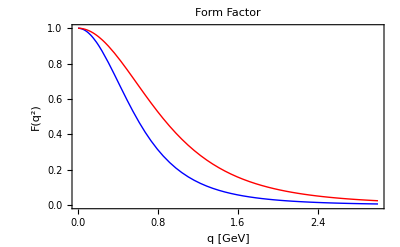

```mathematica
Plot[{FF[q,0.9],FF[q,1.3]},{q,0,3},Frame->True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotLabel->"Form Factor",FrameLabel->{"q [GeV]","F(q^2)"}]
```

Form factor appears as the form factor squared in the Fock terms.

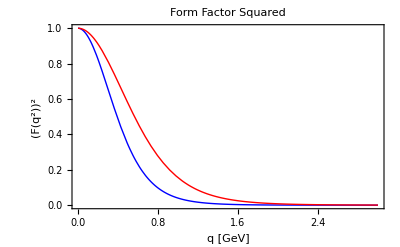

```mathematica
Plot[{FF[q,0.9]^2,FF[q,1.3]^2},{q,0,3},Frame->True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotLabel->"Form Factor Squared",FrameLabel->{"q [GeV]","(F(q^2))^2"}]
```

## Main Input Parameters

```mathematica
hbc=197.327053`20;
ρ0 = 0.16`20;
BE0 = -15.865`20/hbc;
S0 = 30 / hbc;
mπ=139.57`20/hbc;
gA = 1.26`20;
fπ=93/hbc;
```

```mathematica
Gσ = 11.33`20; (*fm^2*)
Gω = 7.27`20;
Gρ = 4.56`20;
```

```mathematica
mσ = 700/hbc;
mω =782.6`20/hbc;
mρ =775.8`20/hbc;
```

```mathematica
gσ = √(Gσ mσ^2)
```

11.9406059095148843

```mathematica
gω = √(Gω mω^2)
```

10.69351342686804167

```mathematica
gρ = √(Gρ mρ^2)
```

8.395480682444379522

```mathematica
σ0 = 20/hbc;(* a rough guess of scalar field at saturation*)
```

## Nucleon Mass Parametrisation

```mathematica
MN=939/hbc;
RNFREE = 0.8`20;
```

Note that the 2006 and 2008 papers write the mass parametrisation slightly differently (Same value for nucleon):
2006:
M^*= M- g_σ σ+d/2(g_σ σ)^2 with d = 0.0044 + 0.211 R_B-0.0357 R_B^2
2008
M^*= M -g_σ σ + (0.002143 + 0.10562 R_B-0.01791 R_B^2)(g_σ σ)^2

```mathematica
d2008[RN_?NumericQ]:= SetPrecision[(0.002143`20+0.10562`20RN-0.01791`20 RN^2)2,WP];
```

```mathematica
d2006 = 0.0044`16 +0.211`16 RNFREE -0.0357`16 RNFREE^2
```

0.150352

```mathematica
MNS[σbar_?NumericQ,GσL_?NumericQ]:=SetPrecision[Module[{MNStar,gσL},
gσL = √(GσL mσ^2);
MNStar = MN - gσL σbar + d2008[RNFREE]/2(gσL σbar)^2;
Return[MNStar];
],WP];
DMDS[σbar_?NumericQ,GσL_?NumericQ]:= SetPrecision[Module[{DMDSstar,gσL},
gσL =√(GσL mσ^2);
DMDSstar=-gσL + d2008[RNFREE] gσL^2 σbar;
Return[DMDSstar];
],WP];
```

```mathematica
Precision[d2008[RNFREE]]
```

16.

```mathematica
Precision[MNS[20/hbc,Gσ]hbc]
```

16.

```mathematica
Precision[DMDS[20/hbc,Gσ]]
```

16.

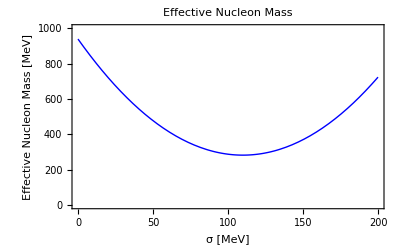

```mathematica
Plot[MNS[σ/hbc,Gσ] hbc ,{σ,0,200},Frame->True,PlotRange-> {0,1000},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},PlotStyle-> {Thick,Blue},PlotLabel-> "Effective Nucleon Mass",FrameLabel-> {" σ [MeV]","Effective Nucleon Mass [MeV]"},Background-> White]
```

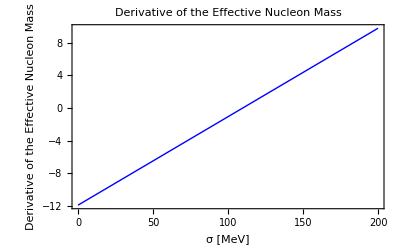

```mathematica
Plot[DMDS[σ/hbc,Gσ] ,{σ,0,200},Frame->True,BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},PlotStyle-> {Thick,Blue},PlotLabel-> "Derivative of the Effective Nucleon Mass",FrameLabel-> {" σ [MeV]","Derivative of the Effective Nucleon Mass "},Background-> White]
```

## Solving for the scalar field

```mathematica
Integrate[k^2/(√(k^2+MS^2)),{k,0,kf},Assumptions -> kf>0 && MS>0]
```

1/2 (kf √(kf^2+MS^2)-MS^2 ArcTanh[kf/(√(kf^2+MS^2))])

```mathematica
SigmaHelper[kfN_?NumericQ,σ_?NumericQ,GσL_?NumericQ]:= SetPrecision[-1/mσ^2(2/(2 π)^3 4π MNS[σ,GσL] DMDS[σ,GσL])(1/2 (kfN √(kfN^2+MNS[σ,GσL]^2)-MNS[σ,GσL]^2 ArcSinh[kfN/MNS[σ,GσL]])),WP];
```

```mathematica
Precision[SigmaHelper[1.33`20,σ0,Gσ]]
```

16.

```mathematica
FSigma[ρn_?NumericQ,ρp_?NumericQ,msigOpt_,GσL_?NumericQ,ΛσGeV_]:= Module[{GuessSigma,CurSol,σsol,kfn,kfp},

kfn = (3 π^2 ρn)^(1/3);
kfp = (3 π^2 ρp)^(1/3);

GuessSigma = σ0;

CurSol = FindRoot[

σ == SigmaHelper[kfn,σ,GσL] +SigmaHelper[kfp,σ,GσL] (*-1/mσ^2DϵσFDσ[ρn,ρp,σ,msigOpt,GσL,ΛσGeV]/hbc*),

{σ,GuessSigma},WorkingPrecision->WP,MaxIterations->1000];

σsol=σ /. CurSol;

Return[σsol];
];
```

Note the positive sign convention for the scalar field.

```mathematica
FSigma[ρ0/2,ρ0/2,"Effρv",Gσ,∞]hbc
```

22.795945206959

```mathematica
Precision[FSigma[ρ0/2,ρ0/2,"Effρv",Gσ,∞]hbc]
```

16.

## Scalar density

```mathematica
ρsHelper[kfN_?NumericQ,σ_?NumericQ,GσL_?NumericQ]:= (2/(2 π)^3 4π MNS[σ,GσL] )(1/2 (kfN √(kfN^2+MNS[σ,GσL]^2)-MNS[σ,GσL]^2 ArcSinh[kfN/MNS[σ,GσL]]))
```

```mathematica
Fρs[ρn_?NumericQ,ρp_?NumericQ,msigOpt_,GσL_?NumericQ,ΛσGeV_]:= Module[{Sigma,CurSol,σsol,kfn,kfp},

Sigma=FSigma[ρn,ρp,msigOpt,GσL,ΛσGeV];

kfn = (3 π^2 ρn)^(1/3);
kfp = (3 π^2 ρp)^(1/3);

ρs = SetPrecision[ρsHelper[kfn,Sigma,GσL]+ρsHelper[kfp,Sigma,GσL],WP];

Return[ρs];
];
```

```mathematica
Fρs[ρ0/2,ρ0/2,"Effρv",Gσ,∞]
```

0.1536079496303578

```mathematica
Precision[Fρs[ρ0/2,ρ0/2,"Effρv",Gσ,∞]]
```

16.

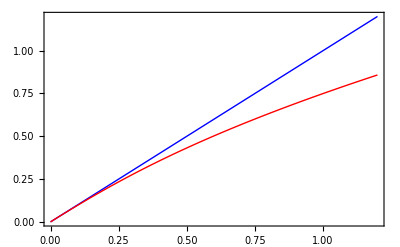

```mathematica
Plot[{ρ,Fρs[ρ/2,ρ/2,"Effρv",Gσ,∞]},{ρ,0,1.2`20},Frame->True,PlotStyle->{{Thick,Blue},{Thick,Red}}]
```

## Fock Term Functions

### Functions for the omega, rho and pi mesons

```mathematica
Jffhelper[k1_?NumericQ,kf2_?NumericQ,m_?NumericQ]:=NIntegrate[k1 k2 Log[((k1 + k2)^2+m^2)/((k1 - k2)^2+m^2)],{k2,0,kf2},WorkingPrecision->WP,Method->{Automatic,"SymbolicProcessing"->0}];


Jff[kf1_?NumericQ,kf2_?NumericQ,m_?NumericQ]:=If[kf1>0 && kf2>0,-(4 π^2)/(2π)^6 m^2 NIntegrate[Jffhelper[k1,kf2,m],{k1,0,kf1},WorkingPrecision->WP,Method->{Automatic,"SymbolicProcessing"->0}],0];
```

### Functions for the omega, rho and pi mesons with form factors included

The first part of the integrand in brackets ( .. )^4is the part corresponding to the form factor. To check that it gives the same when Λ->∞, just remove this and run again. It should give the same within the numerical precision. Note that without this term the angular integral can be done exactly, which has been done in the other methods above.

```mathematica
JffInnerhelperwithFF[k1_?NumericQ,k2_?NumericQ,m_?NumericQ,Λ_?NumericQ]:=NIntegrate[ (1/(1+(k1^2+k2^2-2 k1 k2 X)/Λ^2))^4(k1 k2)^2/(k1^2+k2^2-2 k1 k2 X +m^2),{X,1,-1},WorkingPrecision->WP,Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
JffhelperwithFF[k1_?NumericQ,kf2_?NumericQ,m_?NumericQ,Λ_?NumericQ]:=NIntegrate[JffInnerhelperwithFF[k1,k2,m,Λ],{k2,0,kf2},WorkingPrecision->WP,Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
JffwithFF[kf1_?NumericQ,kf2_?NumericQ,m_?NumericQ,Λ_?NumericQ]:=If[kf1>0 && kf2>0,(8 π^2)/(2π)^6 m^2 NIntegrate[JffhelperwithFF[k1,kf2,m,Λ],{k1,0,kf1},WorkingPrecision->WP,Method->{Automatic,"SymbolicProcessing"->0}],0];
```

### Functions for the sigma meson

```mathematica
Jσffhelper[k1_?NumericQ,kf2_?NumericQ,msig_?NumericQ,σbar_?NumericQ,GσL_?NumericQ]:=NIntegrate[1/(√(k1^2+MNS[σbar,GσL]^2)√(k2^2+MNS[σbar,GσL]^2))k1 k2 Log[((k1 + k2)^2+msig^2)/((k1 - k2)^2+msig^2)],{k2,0,kf2},WorkingPrecision->WP,Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
Jσff[kf1_?NumericQ,kf2_?NumericQ,msig_?NumericQ,σbar_?NumericQ,GσL_?NumericQ]:=If[kf1>0 && kf2>0,+(4 π^2)/(2π)^6 NIntegrate[Jσffhelper[k1,kf2,msig,σbar,GσL],{k1,0,kf1},WorkingPrecision->WP,Method->{Automatic,"SymbolicProcessing"->0}],0];
```

### Functions for the sigma meson with form factor

The first part of the integrand in brackets ( .. )^4is the part corresponding to the form factor. To check that it gives the same when Λ->∞, just remove this and run again. It should give the same within the numerical precision. Note that without this term the angular integral can be done exactly, which has been done in the other methods above.

```mathematica
JσffInnerhelperwithFF[k1_?NumericQ,k2_?NumericQ,msig_?NumericQ,σbar_?NumericQ,GσL_?NumericQ,Λ_?NumericQ]:=NIntegrate[ (1/(1+(k1^2+k2^2-2 k1 k2 X)/Λ^2))^4 1/(√(k1^2+MNS[σbar,GσL]^2)√(k2^2+MNS[σbar,GσL]^2))(k1 k2)^2/(k1^2+k2^2-2 k1 k2 X +msig^2),{X,1,-1},WorkingPrecision->WP,Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
JσffhelperwithFF[k1_?NumericQ,kf2_?NumericQ,msig_?NumericQ,σbar_?NumericQ,GσL_?NumericQ,Λ_?NumericQ]:=NIntegrate[JσffInnerhelperwithFF[k1,k2,msig,σbar,GσL,Λ],{k2,0,kf2},WorkingPrecision->WP,Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
JσffwithFF[kf1_?NumericQ,kf2_?NumericQ,msig_?NumericQ,σbar_?NumericQ,GσL_?NumericQ,Λ_?NumericQ]:=If[kf1>0 && kf2>0,-(8 π^2)/(2π)^6 NIntegrate[JσffhelperwithFF[k1,kf2,msig,σbar,GσL,Λ],{k1,0,kf1},WorkingPrecision->WP,Method->{Automatic,"SymbolicProcessing"->0}],0];
```

### Sigma Fock Term functions

Using the non-relativistic approximation for the effective sigma mass and, i.e., Eq. 23 in Nucl. Phys. A772 (2006) 1-19

```mathematica
mσEffρv[ρn_?NumericQ,ρp_?NumericQ,GσL_?NumericQ]:= Module[{ρBL,mσEff},
ρBL = ρn +ρp;
mσEff=SetPrecision[√(mσ^2(1+GσL d2008[RNFREE] ρBL)),WP];
Return[mσEff];
];
mσEffρs[ρn_?NumericQ,ρp_?NumericQ,GσL_?NumericQ,ΛσGeV_]:= Module[{ρsL,mσEff},
ρsL = Fρs[ρn,ρp,"Effρs",GσL,ΛσGeV]; 
mσEff=SetPrecision[√(mσ^2(1+GσL d2008[RNFREE] ρsL)),WP];
Return[mσEff];
];
Effmσ[mσOpt_,ρn_?NumericQ,ρp_?NumericQ,GσL_?NumericQ,ΛσGeV_]:=Switch[mσOpt,
"FREE",mσ,
"Effρv",mσEffρv[ρn,ρp,GσL],
"Effρs",mσEffρs[ρn,ρp,GσL,ΛσGeV],
_,"ERROR THIS IS NOT AN OPTION FOR Effmσ ! ! !"];
```

```mathematica
Effmσ["FREE",ρ0/2,ρ0/2,Gσ,∞]hbc
```

700.

Precision is not 20., because of the multiplication by hbc

```mathematica
Precision[Effmσ["FREE",ρ0/2,ρ0/2,Gσ,∞]hbc]
```

19.699

```mathematica
Effmσ["Effρv",ρ0/2,ρ0/2,Gσ,∞]hbc
```

789.654695212027

```mathematica
Precision[Effmσ["Effρv",ρ0/2,ρ0/2,Gσ,∞]hbc]
```

16.

```mathematica
Effmσ["Effρs",ρ0/2,ρ0/2,Gσ,∞]hbc
```

786.269032740148

```mathematica
Precision[Effmσ["Effρs",ρ0/2,ρ0/2,Gσ,∞]hbc]
```

16.

This is what happens if you enter something else, NO error handling included. This is common through out so BEWARE !!

```mathematica
Effmσ["SOMETHING ELSE",ρ0/2,ρ0/2,Gσ]hbc
```

197.327053 Effmσ[SOMETHING ELSE,0.08,0.08,11.33]

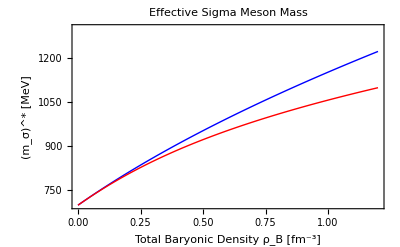

```mathematica
Plot[{mσEffρv[ρ/2,ρ/2,Gσ]hbc ,mσEffρs[ρ/2,ρ/2,Gσ,∞]hbc},{ρ,0,1.2`20},Frame->True, 
FrameLabel -> {" Total Baryonic Density ρ_B [fm^-3] "," (m_σ)^* [MeV] "},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Blue},{Thick,Red}},PlotLabel-> " Effective Sigma Meson Mass ",PlotRange-> {mσ hbc,1300.},Background->White]
```

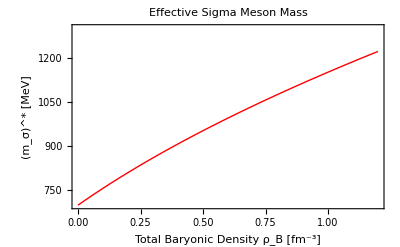

```mathematica
Plot[mσEffρv[ρ/2,ρ/2,Gσ]hbc ,{ρ,0,1.2`20},Frame->True, 
FrameLabel -> {" Total Baryonic Density ρ_B [fm^-3] "," (m_σ)^* [MeV] "},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {Thick,Red,Dashing},PlotLabel-> " Effective Sigma Meson Mass ",PlotRange-> {mσ hbc,1300.},Background->White]
```

```mathematica
ϵσF[ρn_?NumericQ,ρp_?NumericQ,σbar_?NumericQ,msig_?NumericQ,GσL_?NumericQ,ΛσGeV_]:= Module[{kfn,kfp,σFockTerm,Λ},

kfn = (3 π^2 ρn)^(1/3);
kfp = (3 π^2 ρp)^(1/3);
Λ = ΛσGeV 1000/hbc;
Switch[Λ,
0,σFockTerm=0;,
∞,σFockTerm = SetPrecision[(MNS[σbar,GσL]DMDS[σbar,GσL])^2 (Jσff[kfn,kfn,msig,σbar,GσL]+Jσff[kfp,kfp,msig,σbar,GσL]),WP];,
_Real,σFockTerm = SetPrecision[(MNS[σbar,GσL]DMDS[σbar,GσL])^2 (JσffwithFF[kfn,kfn,msig,σbar,GσL,Λ]+JσffwithFF[kfp,kfp,msig,σbar,GσL,Λ]),WP];];

Return[σFockTerm];
];
```

The value at saturation assuming a scalar field of 20 MeV

```mathematica
ϵσF[ρ0/2,ρ0/2,σ0,mσ,Gσ,0] hbc
```

0

```mathematica
ϵσF[ρ0/2,ρ0/2,σ0,mσ,Gσ,∞] hbc
```

3.83122144942116

```mathematica
Precision[ϵσF[ρ0/2,ρ0/2,σ0,mσ,Gσ,∞] hbc]
```

16.

```mathematica
ϵσF[ρ0/2,ρ0/2,σ0,mσ,Gσ,0.9`20] hbc
```

2.74507946117788

```mathematica
ϵσF[ρ0/2,ρ0/2,σ0,mσ,Gσ,1.3`20] hbc
```

3.22885834598915

```mathematica
Precision[ϵσF[ρ0/2,ρ0/2,σ0,mσ,Gσ,1.3`20] hbc]
```

16.

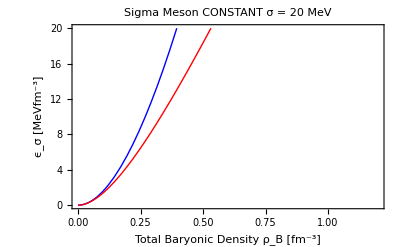

```mathematica
Plot[{ϵσF[ρ/2,ρ/2,σ0,Effmσ["FREE",ρ/2,ρ/2,Gσ,∞],Gσ,∞]hbc,ϵσF[ρ/2,ρ/2,σ0,Effmσ["Effρv",ρ/2,ρ/2,Gσ,∞],Gσ,∞]hbc},{ρ,0,1.2`20},Frame->True, 
FrameLabel -> {"Total Baryonic Density ρ_B [fm^-3]"," ϵ_σ [MeVfm^-3] "},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Blue},{Thick,Red}},PlotLabel-> " Sigma Meson CONSTANT σ = 20 MeV ",PlotRange-> {0.,20.},Background->White]
```

With FF Λ=0.9 GeV, note that coupling should be refit

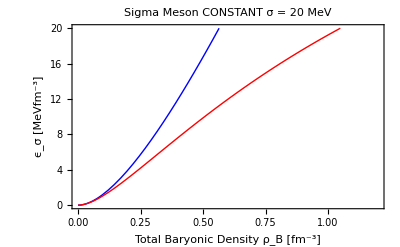

```mathematica
Plot[{ϵσF[ρ/2,ρ/2,σ0,Effmσ["FREE",ρ/2,ρ/2,Gσ,0.9`20],Gσ,0.9`20]hbc,ϵσF[ρ/2,ρ/2,σ0,Effmσ["Effρv",ρ/2,ρ/2,Gσ,0.9`20],Gσ,0.9]hbc},{ρ,0,1.2},Frame->True, 
FrameLabel -> {"Total Baryonic Density ρ_B [fm^-3]"," ϵ_σ [MeVfm^-3] "},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Blue},{Thick,Red}},PlotLabel-> " Sigma Meson CONSTANT σ = 20 MeV ",PlotRange-> {0.,20.},Background->White]
```

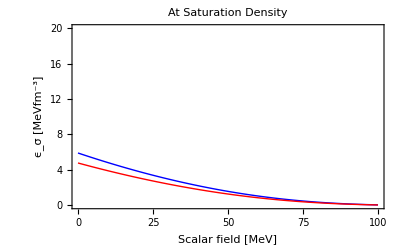

```mathematica
Plot[{ϵσF[ρ0/2,ρ0/2,σ/hbc,Effmσ["FREE",ρ0/2,ρ0/2,Gσ,∞],Gσ,∞]hbc,ϵσF[ρ0/2,ρ0/2,σ/hbc,Effmσ["Effρv",ρ0/2,ρ0/2,Gσ,∞],Gσ,∞]hbc},{σ,0,100},Frame->True, 
FrameLabel -> {"Scalar field [MeV]"," ϵ_σ [MeVfm^-3] "},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Blue},{Thick,Red}},PlotLabel-> "At Saturation Density",PlotRange-> {0.,20.},Background->White]
```

Likewise with FF but coupling should be refit

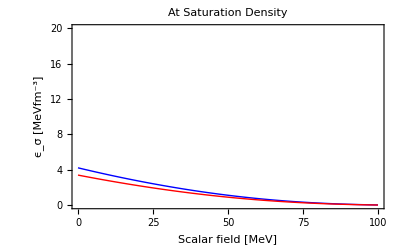

```mathematica
Plot[{ϵσF[ρ0/2,ρ0/2,σ/hbc,Effmσ["FREE",ρ0/2,ρ0/2,Gσ,0.9`20],Gσ,0.9`20]hbc,ϵσF[ρ0/2,ρ0/2,σ/hbc,Effmσ["Effρv",ρ0/2,ρ0/2,Gσ,0.9`20],Gσ,0.9`20]hbc},{σ,0,100},Frame->True, 
FrameLabel -> {"Scalar field [MeV]"," ϵ_σ [MeVfm^-3] "},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Blue},{Thick,Red}},PlotLabel-> "At Saturation Density",PlotRange-> {0.,20.},Background->White]
```

This is used if you want to include a Fock correction to the scalar field. Only the sigma Fock term here has a scalar dependence.

```mathematica
DϵσFDσ[ρn_?NumericQ,ρp_?NumericQ,σ_?NumericQ,mσOpt_,GσL_?NumericQ,ΛσGeV_]:= Module[{DϵσFDσL=0,δσ=0.0001`20,σm1,σm2,σp1,σp2,ϵσFm2,ϵσFm1,ϵσFp1,ϵσFp2},


σm2 = σ-2 δσ;
ϵσFm2 =ϵσF[ρn,ρp,σm2,Effmσ[mσOpt,ρn,ρp,GσL,ΛσGeV],GσL,ΛσGeV];
σm1 = σ-δσ;
ϵσFm1 =ϵσF[ρn,ρp,σm1,Effmσ[mσOpt,ρn,ρp,GσL,ΛσGeV],GσL,ΛσGeV];
σp1 = σ+ δσ;
ϵσFp1 =ϵσF[ρn,ρp,σp1,Effmσ[mσOpt,ρn,ρp,GσL,ΛσGeV],GσL,ΛσGeV];
σp2 = σ +2δσ;
ϵσFp2 =ϵσF[ρn,ρp,σp2,Effmσ[mσOpt,ρn,ρp,GσL,ΛσGeV],GσL,ΛσGeV];
DϵσFDσL = SetPrecision[(-ϵσFp2 +8ϵσFp1 -8 ϵσFm1 +ϵσFm2)/(12 δσ)hbc,WP];



Return[DϵσFDσL];
];
```

```mathematica
DϵσFDσ[ρ0/2,ρ0/2,σ0,"Effρv",Gσ,∞]
```

-14.77990162339221

```mathematica
Precision[DϵσFDσ[ρ0/2,ρ0/2,σ0,"Effρv",Gσ,∞]]
```

16.

### Omega Fock Term

```mathematica
ϵωF[ρn_?NumericQ,ρp_?NumericQ,GωL_?NumericQ,ΛωGeV_]:= Module[{kfn,kfp,ωFockTerm,Λ},

kfn = (3 π^2 ρn)^(1/3);
kfp = (3 π^2 ρp)^(1/3);
Λ = ΛωGeV 1000/hbc;
Switch[Λ,
0,ωFockTerm=0;,
∞,ωFockTerm =  SetPrecision[GωL Jff[kfn,kfn,mω]+GωL Jff[kfp,kfp,mω],WP];
,_Real,ωFockTerm =  SetPrecision[GωL JffwithFF[kfn,kfn,mω,Λ]+GωL JffwithFF[kfp,kfp,mω,Λ],WP];
];


Return[ωFockTerm];
];
```

The value at saturation

```mathematica
ϵωF[ρ0/2,ρ0/2,Gω,0] hbc
```

0

```mathematica
ϵωF[ρ0/2,ρ0/2,Gω,∞] hbc
```

-4.06638532441424

```mathematica
Precision[ϵωF[ρ0/2,ρ0/2,Gω,∞] hbc]
```

16.

```mathematica
ϵωF[ρ0/2,ρ0/2,Gω,0.9`20] hbc
```

-2.89736216871294

```mathematica
Precision[ϵωF[ρ0/2,ρ0/2,Gω,0.9`20] hbc]
```

16.

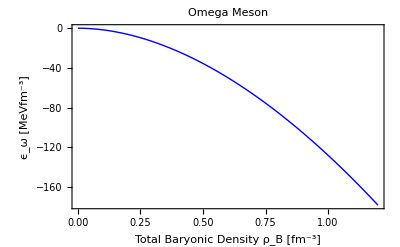

```mathematica
Plot[ϵωF[ρ/2,ρ/2,Gω,∞]hbc,{ρ,0,1.2`20},Frame->True, 
FrameLabel -> {"Total Baryonic Density ρ_B [fm^-3]"," ϵ_ω [MeVfm^-3]"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Blue}},PlotLabel-> " Omega Meson ",PlotRange-> {0.,-180},Background->White]
```

With FF but the couplng should be refit

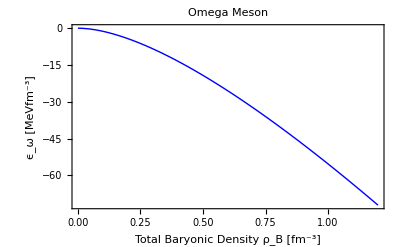

```mathematica
Plot[ϵωF[ρ/2,ρ/2,Gω,0.9`20]hbc,{ρ,0,1.2`20},Frame->True, 
FrameLabel -> {"Total Baryonic Density ρ_B [fm^-3]"," ϵ_ω [MeVfm^-3]"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Blue}},PlotLabel-> " Omega Meson ",PlotRange-> {0.,-180},Background->White]
```

### Rho Fock Term

```mathematica
ϵρF[ρn_?NumericQ,ρp_?NumericQ,GρL_?NumericQ,ΛρGeV_]:= Module[{kfn,kfp,ρFockTerm,Λ},
kfn = (3 π^2 ρn)^(1/3);
kfp = (3 π^2 ρp)^(1/3);
Λ=ΛρGeV 1000/hbc;
Switch[Λ,
0,ρFockTerm=0;,
∞,ρFockTerm = SetPrecision[GρL 1/4( Jff[kfn,kfn,mρ]+4 Jff[kfn,kfp,mρ]+Jff[kfp,kfp,mρ]),WP];
,_Real,ρFockTerm = SetPrecision[GρL 1/4( JffwithFF[kfn,kfn,mρ,Λ]+4 JffwithFF[kfn,kfp,mρ,Λ]+JffwithFF[kfp,kfp,mρ,Λ]),WP];
];

Return[ρFockTerm];
];
```

The value at saturation

```mathematica
ϵρF[ρ0/2,ρ0/2,Gρ,0] hbc
```

0

```mathematica
ϵρF[ρ0/2,ρ0/2,Gρ,∞] hbc
```

-1.90926694516417

```mathematica
Precision[ϵρF[ρ0/2,ρ0/2,Gρ,∞] hbc]
```

16.

Of course the coupling needs to be readjusted.

```mathematica
ϵρF[ρ0/2,ρ0/2,Gρ,0.9`20] hbc
```

-1.3607238541895

```mathematica
Precision[ϵρF[ρ0/2,ρ0/2,Gρ,0.9`20] hbc]
```

16.

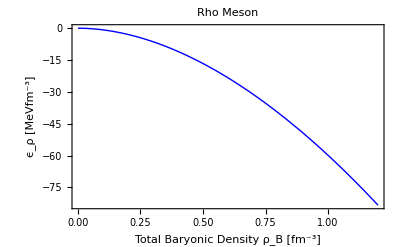

```mathematica
Plot[ϵρF[ρ/2,ρ/2,Gρ,∞]hbc,{ρ,0,1.2`20},Frame->True, 
FrameLabel -> {"Total Baryonic Density ρ_B [fm^-3]"," ϵ_ρ [MeVfm^-3]"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Blue}},PlotLabel-> " Rho Meson ",PlotRange-> {0.,-180},Background->White]
```

With FF but coupling should be refit

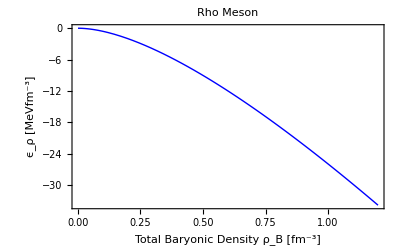

```mathematica
Plot[ϵρF[ρ/2,ρ/2,Gρ,0.9`20]hbc,{ρ,0,1.2`20},Frame->True, 
FrameLabel -> {"Total Baryonic Density ρ_B [fm^-3]"," ϵ_ρ [MeVfm^-3]"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Blue}},PlotLabel-> " Rho Meson ",PlotRange-> {0.,-180},Background->White]
```

### Pion Fock Term

```mathematica
ϵπF[ρn_?NumericQ,ρp_?NumericQ,ΛπGeV_]:= Module[{kfn,kfp,πFockTerm,Λ},

kfn = (3 π^2 ρn)^(1/3);
kfp = (3 π^2 ρp)^(1/3);
Λ=ΛπGeV 1000/hbc;
Switch[Λ,
0,πFockTerm=0;,
∞,
πFockTerm = SetPrecision[(gA/(2 fπ))^2( Jff[kfn,kfn,mπ]+4 Jff[kfn,kfp,mπ]+Jff[kfp,kfp,mπ]),WP];
,_Real,πFockTerm = SetPrecision[(gA/(2 fπ))^2( JffwithFF[kfn,kfn,mπ,Λ]+4 JffwithFF[kfn,kfp,mπ,Λ]+JffwithFF[kfp,kfp,mπ,Λ]),WP];
];
Return[πFockTerm];
];
```

Value at saturation

```mathematica
ϵπF[ρ0/2,ρ0/2,0] hbc
```

0

```mathematica
ϵπF[ρ0/2,ρ0/2,∞] hbc
```

-0.894963367069797

```mathematica
Precision[ϵπF[ρ0/2,ρ0/2,∞] hbc]
```

16.

```mathematica
ϵπF[ρ0/2,ρ0/2,0.9`20] hbc
```

-0.708422664649193

```mathematica
ϵπF[ρ0/2,ρ0/2,1.3`20] hbc
```

-0.794003028142186

```mathematica
Precision[ϵπF[ρ0/2,ρ0/2,1.3`20] hbc]
```

16.

Can do this plot for the pion because the known value of the coupling g_A is used and does not depend on the form factor cut-off used. For the other mesons it is necessary to refit the couplings when changing Λ.

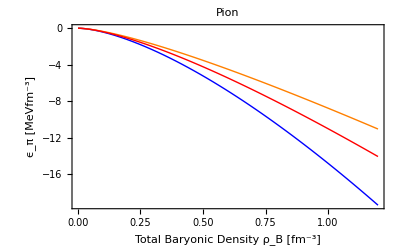

```mathematica
Plot[{ϵπF[ρ/2,ρ/2,∞]hbc,ϵπF[ρ/2,ρ/2,0.9`20]hbc,ϵπF[ρ/2,ρ/2,1.3`20]hbc},{ρ,0,1.2`20},Frame->True, 
FrameLabel -> {"Total Baryonic Density ρ_B [fm^-3]"," ϵ_π [MeVfm^-3]"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Blue},{Thick,Orange},{Thick,Red}},PlotLabel-> " Pion ",PlotRange-> {0.,-20},Background->White]
```

#### Pion Data (If you want to output to a file)

```mathematica
δxρ=0.01`20; (* Note δρ used for numerical derivatives *)
```

```mathematica
Data=TableForm[Table[{δxρ n,ϵπF[δxρ n /2,δxρ n /2,∞]hbc},{n,120}],TableHeadings->{None,{" ρ_B [fm^-3] "," ϵ_π [MeVfm^-3] "}}];
```

```mathematica
PathToFile=StringJoin[PathToCalcData,"/PionFockTerm.dat"];
```

```mathematica
Export[PathToFile,Data,"Table"];
```

## Hartree Contributions to the Energy Density

### Baryon Contribution

```mathematica
Integrate[k^2 √(k^2+MS^2),{k,0,kf},Assumptions->kf> 0 && MS> 0]
```

1/8 (kf √(kf^2+MS^2) (2 kf^2+MS^2)-MS^4 ArcSinh[kf/MS])

```mathematica
ϵBhelper[kfN_?NumericQ,σbar_?NumericQ,GσL_?NumericQ]:=SetPrecision[2/(2π)^3 4π(1/8 (kfN √(kfN^2+MNS[σbar,GσL]^2) (2 kfN^2+MNS[σbar,GσL]^2)-MNS[σbar,GσL]^4 ArcSinh[kfN/MNS[σbar,GσL]])),WP];
```

```mathematica
Precision[ϵBhelper[1.33`20,σ0,Gσ]]
```

16.

```mathematica
ϵB[ρn_?NumericQ,ρp_?NumericQ,σbar_?NumericQ,GσL_?NumericQ]:= Module[{kfn,kfp,ϵBaryon},

kfn = (3 π^2 ρn)^(1/3);
kfp = (3 π^2 ρp)^(1/3);
ϵBaryon = ϵBhelper[kfn,σbar,GσL] +ϵBhelper[kfp,σbar,GσL];

Return[ϵBaryon];
];
```

Value at saturation assuming σ = 20 MeV

```mathematica
ϵB[ρ0/2,ρ0/2,20/hbc,Gσ]hbc
```

120.003133959538

```mathematica
Precision[ϵB[ρ0/2,ρ0/2,20/hbc,Gσ]hbc]
```

16.

```mathematica
ϵσH[σbar_?NumericQ]:=1/2 mσ^2 σbar^2;
```

```mathematica
ϵσH[20/hbc]hbc
```

12.75458069842643392

```mathematica
Precision[ϵσH[20/hbc]hbc]
```

19.301

```mathematica
ϵωH[ρn_?NumericQ,ρp_?NumericQ,GωL_?NumericQ]:= GωL/2(ρn+ρp)^2;
```

```mathematica
ϵωH[ρ0/2,ρ0/2,Gω]hbc
```

18.362466243968

```mathematica
Precision[ϵωH[ρ0/2,ρ0/2,Gω]hbc]
```

19.3979

```mathematica
ϵρH[ρn_?NumericQ,ρp_?NumericQ,GρL_?NumericQ]:=  Module[{ρHartree},
ρHartree = GρL/8(ρp-ρn)^2;
Return[ρHartree];
];
```

```mathematica
ϵρH[ρ0/2,ρ0/2,Gρ]hbc
```

0.

```mathematica
ϵρH[ρ0,0,Gρ]hbc
```

2.879396357376

```mathematica
ϵρH[0,ρ0,Gρ]hbc
```

2.879396357376

```mathematica
Precision[ϵρH[0,ρ0,Gρ]hbc]
```

19.3979

## Total Energy Density

```mathematica
ϵTotal[ρn_?NumericQ,ρp_?NumericQ,msigOpt_,GσL_?NumericQ,GωL_?NumericQ,GρL_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_]:= Module[{TotalEnDen,σbar,msig},
σbar=FSigma[ρn,ρp,msigOpt,GσL,ΛσGeV];
msig =Effmσ[msigOpt,ρn,ρp,GσL,ΛσGeV];
TotalEnDen = SetPrecision[( ϵB[ρn,ρp,σbar,GσL] +ϵσH[σbar]+ϵωH[ρn,ρp,GωL]+ϵρH[ρn,ρp,GρL]+ϵσF[ρn,ρp,σbar,msig,GσL,ΛσGeV]+ϵωF[ρn,ρp,GωL,ΛωGeV]+ϵρF[ρn,ρp,GρL,ΛρGeV] +ϵπF[ρn,ρp,ΛπGeV]),WP];
Return[TotalEnDen];
];
```

Value of total energy density at saturation

```mathematica
ϵTotal[ρ0/2,ρ0/2,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]hbc
```

147.715612642761

```mathematica
Precision[ϵTotal[ρ0/2,ρ0/2,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]hbc]
```

16.

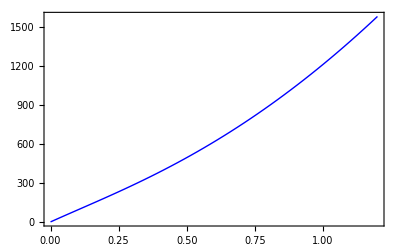

```mathematica
Plot[ϵTotal[ρ/2,ρ/2,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0] hbc ,{ρ,0,1.2`20},PlotStyle-> {Thick,Blue},Frame->True]
```

## Binding Energy

```mathematica
BindingEnergy[ρ_?NumericQ,msigOpt_,GσL_?NumericQ,GωL_?NumericQ,GρL_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_]:= Module[{ρn,ρp,BE},
ρn =ρ/2;
ρp = ρ/2;
BE=SetPrecision[ϵTotal[ρn,ρp,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]/ρ  -MN ,WP];

Return[BE];
];
```

```mathematica
BindingEnergy[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]hbc
```

-15.777420982746

```mathematica
Precision[BindingEnergy[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]hbc]
```

16.

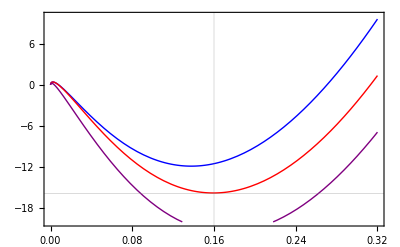

```mathematica
Plot[{BindingEnergy[ρ,"FREE",Gσ,Gω,Gρ,∞,∞,∞,0]hbc,BindingEnergy[ρ,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]hbc,BindingEnergy[ρ,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,∞]hbc} ,{ρ,0,2 ρ0},PlotRange->{-20,10},PlotStyle-> {{Thick,Blue},{Thick,Red},{Thick,Purple}},GridLines->{{ρ0},{BE0 hbc}},Frame->True]
```

Note that it is a little off from where it should be, but this is most likely because I don't know what values Guichon used for the meson masses and so it is bound to be a little different. Also I am using rounded off values for the couplings as quoted in the paper. This too would result in slight differences. There may be a difference in how the effective sigma meson mass is calculated. Here I have used the non-relativistic approximation.

Syntax: GridLines → {{Vertical Line 1, Vertical Line 2}, {Horizontal Line 1, ........}}

```mathematica
DerivativeOfBindingEnergy[ρ_?NumericQ,msigOpt_,GσL_?NumericQ,GωL_?NumericQ,GρL_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_]:= Module[{δρ,ρn,ρp,ρm1,ρm2,ρp1,ρp2,DBEDρ,BEm1,BEm2,BEp1,BEp2,σm2,σm1,σp1,σp2,BE},
(* Central difference formula. Truncation error O(Δx^4) *)

δρ = 0.001`20;

(* i - 2 *)
ρm2 = (ρ-2 δρ);
ρn =ρm2/2;
ρp = ρm2/2;

BEm2 =BindingEnergy[ρm2,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];


(* i - 1 *)
ρm1 = (ρ-δρ);
ρn =ρm1/2;
ρp = ρm1/2;

BEm1 =BindingEnergy[ρm1,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];


(* i + 1 *)
ρp1 = (ρ+δρ);
ρn =ρp1/2;
ρp = ρp1/2;
BEp1=BindingEnergy[ρp1,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];


(* i + 2 *)
ρp2 = (ρ+2 δρ);
ρn =ρp2/2;
ρp = ρp2/2;

BEp2 = BindingEnergy[ρp2,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];


DBEDρ =SetPrecision[ (-BEp2 + 8 BEp1 -8 BEm1 +BEm2)/(12 δρ),WP];


Return[DBEDρ];
];
```

```mathematica
DerivativeOfBindingEnergy[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]
```

0.004466747525869331

```mathematica
Precision[DerivativeOfBindingEnergy[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]]
```

16.

## Symmetry Energy

```mathematica
SymEnDifference[ρ_?NumericQ,msigOpt_,GσL_?NumericQ,GωL_?NumericQ,GρL_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_]:= Module[{pnm,snm,σpnm,σsnm,msigpnm,msigsnm,SymEn},

pnm =SetPrecision[ϵTotal[ρ,0,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]/ρ hbc -MN hbc,WP];
snm =BindingEnergy[ρ,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]hbc;

SymEn = pnm - snm;


Return[SymEn];
];
```

```mathematica
SymEnDifference[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]
```

31.349046300668

```mathematica
Precision[SymEnDifference[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]]
```

16.

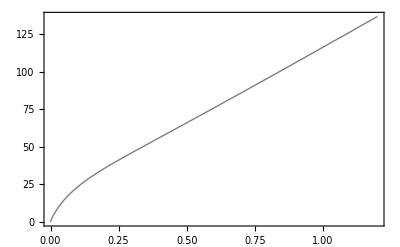

```mathematica
Plot[SymEnDifference[ρ,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0],{ρ,0,1.2`20},Frame->True,PlotStyle->{Thick,Gray}]
```

```mathematica
SymEnNUMERICAL[ρ_?NumericQ,msigOpt_,GσL_?NumericQ,GωL_?NumericQ,GρL_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_]:= Module[{t=0,δt=0.001`20,ρn,ρp,kfn,kfp,tm1,tm2,tp1,tp2,Acur,Am1,Am2,Ap1,Ap2,SymEnNumerical},

ρn = ρ/2;
ρp =ρ/2;

Acur =SetPrecision[ϵTotal[ρn,ρp,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]/ρ hbc,WP];

tm1 = t-δt;
ρn =(ρ/2)(1+tm1);
ρp = (ρ/2)(1-tm1);
Am1=SetPrecision[ϵTotal[ρn,ρp,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]/ρ hbc,WP];

tm2 = t-2 δt;
ρn =(ρ/2)(1+tm2);
ρp = (ρ/2)(1-tm2);
Am2=SetPrecision[ϵTotal[ρn,ρp,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]/ρ hbc,WP];
tp1 = t+ δt;
ρn =(ρ/2)(1+tp1);
ρp = (ρ/2)(1-tp1);
Ap1=SetPrecision[ϵTotal[ρn,ρp,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]/ρ hbc,WP];
tp2 = t + 2 δt;
ρn =(ρ/2)(1+tp2);
ρp = (ρ/2)(1-tp2);
Ap2=SetPrecision[ϵTotal[ρn,ρp,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]/ρ hbc,WP];
SymEnNumerical=SetPrecision[1/2((-Ap2+16Ap1-30Acur+16Am1-Am2)/(12 δt^2)),WP];


Return[SymEnNumerical];
];
```

```mathematica
SymEnNUMERICAL[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]
```

30.13791814369737

```mathematica
Precision[SymEnNUMERICAL[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]]
```

16.

## Slope of the Symmetry Energy

```mathematica
Slope[SymFn_,ρ_?NumericQ,msigOpt_,GσL_?NumericQ,GωL_?NumericQ,GρL_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_]:= Module[{slopeOut,δρ = 0.001`20,ρm1,ρm2,ρp1,ρp2},
ρm1 = ρ-δρ;
ρm2 = ρ-2 δρ;
ρp1 = ρ+ δρ;
ρp2 = ρ + 2 δρ;
slopeOut= SetPrecision[3 ρ 1/(12 δρ)(-SymFn[ρp2,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]+8 SymFn[ρp1,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]-8 SymFn[ρm1,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV] +SymFn[ρm2,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]),WP];
Return[slopeOut];
];
```

```mathematica
Slope[SymEnDifference,ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]
```

57.15973154918957

```mathematica
Precision[Slope[SymEnDifference,ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]]
```

16.

```mathematica
Slope[SymEnNUMERICAL,ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]
```

53.67797626522185

```mathematica
Precision[Slope[SymEnNUMERICAL,ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]]
```

16.

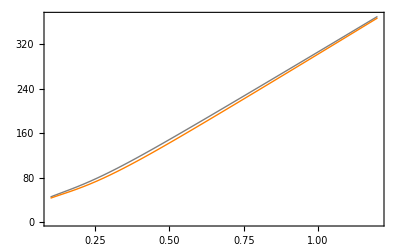

```mathematica
Plot[{Slope[SymEnDifference,ρ,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0],Slope[SymEnNUMERICAL,ρ,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]},{ρ,0.1`20,1.2`20},Frame-> True,PlotStyle->{{Thick,Gray},{Thick,Orange}}]
```

## Pressure SNM

```mathematica
PressureSNM[ρ_?NumericQ,msigOpt_,GσL_?NumericQ,GωL_?NumericQ,GρL_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_]:= Module[{pressureOut,δρ = 0.001`20,ρm1,ρm2,ρp1,ρp2,ρn,ρp,σm1,σm2,σp1,σp2,EnPerPartρm1,EnPerPartρm2,EnPerPartρp1,EnPerPartρp2},
ρm1 = ρ-δρ;
ρn = ρm1/2;
ρp = ρm1/2;

EnPerPartρm1 =SetPrecision[ ϵTotal[ρn,ρp,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]/ρm1 hbc,WP];
ρm2 = ρ-2 δρ;
ρn = ρm2/2;
ρp = ρm2/2;

EnPerPartρm2 = SetPrecision[ϵTotal[ρn,ρp,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]/ρm2 hbc,WP];
ρp1 = ρ+ δρ;
ρn = ρp1/2;
ρp = ρp1/2;

EnPerPartρp1 =SetPrecision[ ϵTotal[ρn,ρp,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]/ρp1 hbc,WP];
ρp2 = ρ + 2 δρ;
ρn = ρp2/2;
ρp = ρp2/2;

EnPerPartρp2 = SetPrecision[ϵTotal[ρn,ρp,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]/ρp2 hbc,WP];
pressureOut =SetPrecision[ ρ^2 1/(12 δρ)(-EnPerPartρp2+8EnPerPartρp1-8 EnPerPartρm1 +EnPerPartρm2),WP];
Return[pressureOut];
];
```

```mathematica
PressureSNM[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]
```

0.02256409921983581

```mathematica
Precision[PressureSNM[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]]
```

16.

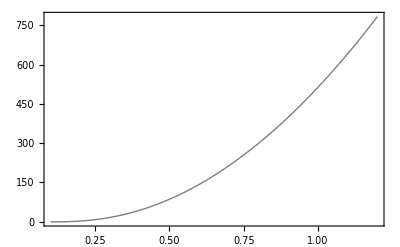

```mathematica
Plot[PressureSNM[ρ,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0],{ρ,0.1`20,1.2`20},PlotStyle->{Thick,Gray},Frame-> True]
```

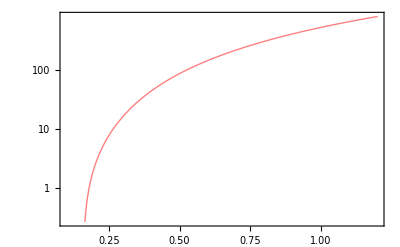

```mathematica
p1=LogPlot[PressureSNM[ρ,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0],{ρ,0.1`20,1.2`20},PlotStyle->{Thick,Pink},Frame-> True]
```

Import Danielewicz data from HIC for the SNM EoS

```mathematica
DanSNMdata=Import[PathToHICData,{"Data",{All}}];
```

```mathematica
DanSNMdata//TableForm
```

0.32 | 7.4
0.36 | 10.5
0.4 | 15.9
0.44 | 20.9
0.48 | 25.8
0.56 | 40.9
0.64 | 55.3
0.72 | 57.1
0.736 | 57.1
0.736 | 209
0.72 | 201
0.64 | 156
0.56 | 116
0.48 | 73.4
0.44 | 56.6
0.4 | 36.8
0.32 | 13.5
0.32 | 7.4

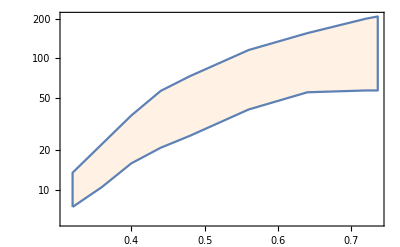

```mathematica
p2=ListLogPlot[DanSNMdata,Filling->Bottom,FillingStyle->Directive[Opacity[0.1],Orange],Joined->True,Frame->True]
```

Compare calculation to HIC data

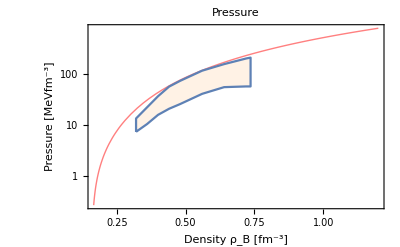

```mathematica
Show[p1,p2,PlotRange->All,PlotLabel-> "Pressure",FrameLabel->{"Density ρ_B [fm^-3]","Pressure [MeVfm^-3]"}]
```

## Incompressibility

```mathematica
Incompressibility[ρ_?NumericQ,msigOpt_,GσL_?NumericQ,GωL_?NumericQ,GρL_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_]:= Module[{K0,DPDρ=0,δρ=0.001`20,ρm1,ρm2,ρp1,ρp2,Pm2,Pm1,Pp1,Pp2},


ρm2 = ρ-2 δρ;
Pm2 =PressureSNM[ρm2,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];
ρm1 = ρ-δρ;
Pm1 =PressureSNM[ρm1,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];
ρp1 = ρ+ δρ;
Pp1 =PressureSNM[ρp1,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];
ρp2 = ρ + 2 δρ;
Pp2 =PressureSNM[ρp2,msigOpt,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];

DPDρ = SetPrecision[(-Pp2 +8Pp1 -8 Pm1 +Pm2)/(12 δρ),WP];

K0 = 9 DPDρ;

Return[K0];
];
```

```mathematica
Incompressibility[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]
```

343.7333480177595

```mathematica
Precision[Incompressibility[ρ0,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0]]
```

16.

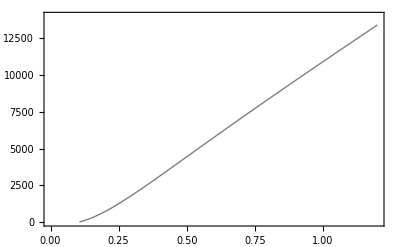

```mathematica
Plot[Incompressibility[ρ,"Effρv",Gσ,Gω,Gρ,∞,∞,∞,0],{ρ,0.1`20,1.2`20},PlotRange->{0,14000},Frame->True,PlotStyle->{Thick,Gray}]
```

## Functions for Fitting Couplings

“Couplings” function uses the difference formula for the symmetry energy, which is an approximation.

```mathematica
Couplings[msigOpt_,GσGuess_?NumericQ,GωGuess_?NumericQ,GρGuess_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_]:= Module[{CurSol,CurSolGσ,CurSolGω,CurSolGρ,CouplingsOutput={},GσNEW,GωNEW,GρNEW},
CurSol=FindRoot[{
BindingEnergy[ρ0,msigOpt,GσNEW,GωNEW,GρNEW,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]hbc== BE0 hbc,
DerivativeOfBindingEnergy[ρ0,msigOpt,GσNEW,GωNEW,GρNEW,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV] ==0,
SymEnDifference[ρ0,msigOpt,GσNEW,GωNEW,GρNEW,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]== S0 hbc},{{GσNEW,GσGuess},{GωNEW,GωGuess},{GρNEW,GρGuess}},WorkingPrecision->WP,MaxIterations->1000];


CurSolGσ = GσNEW/.CurSol[[1]];
CurSolGω= GωNEW /. CurSol[[2]];
CurSolGρ = GρNEW /. CurSol[[3]];

CouplingsOutput = {CurSolGσ,CurSolGω,CurSolGρ};

Return[CouplingsOutput];
];
```

“Couplings2” function uses a numerical difference formula to calculate the symmetry energy.

```mathematica
Couplings2[msigOpt_,GσGuess_?NumericQ,GωGuess_?NumericQ,GρGuess_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_]:= Module[{CurSol,CurSolGσ,CurSolGω,CurSolGρ,CouplingsOutput={},GσNEW,GωNEW,GρNEW},
CurSol=FindRoot[{
BindingEnergy[ρ0,msigOpt,GσNEW,GωNEW,GρNEW,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]hbc== BE0 hbc,
DerivativeOfBindingEnergy[ρ0,msigOpt,GσNEW,GωNEW,GρNEW,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV] ==0,
SymEnNUMERICAL[ρ0,msigOpt,GσNEW,GωNEW,GρNEW,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]== S0 hbc},{{GσNEW,GσGuess},{GωNEW,GωGuess},{GρNEW,GρGuess}},WorkingPrecision->WP,MaxIterations->1000];


CurSolGσ = GσNEW/.CurSol[[1]];
CurSolGω= GωNEW /. CurSol[[2]];
CurSolGρ = GρNEW /. CurSol[[3]];

CouplingsOutput = {CurSolGσ,CurSolGω,CurSolGρ};

Return[CouplingsOutput];
];
```

## Functions for creating an SNM EoS table ( ρ [fm^-3] P [MeV fm^-3] ϵ [MeV fm^-3] (each of the contributions to ϵ aswell))

Given the couplings

```mathematica
EoSTable[mσType_,GσL_?NumericQ,GωL_?NumericQ,GρL_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_,a_?NumericQ,b_?NumericQ,δρ_?NumericQ,NameVariation_?StringQ]:= Module[{BE,ϵTot, pTot, ρ,EoSOut={},EoSRow,EnDenContribOut={},EnDenContribRow,AllData,Path,PathEoS,PathEnDenContrib,σSol,ϵBSol,ϵσHSol,ϵωHSol,ϵρHSol,ϵσFSol,ϵωFSol,ϵρFSol,ϵπFSol,CHECK},



(* ################################################### *)
Do[
(*==========================================*)
(* calculate EoS *)
(*==========================================*)
(* Have parameters, now calculate SNM properties ρn = ρp = ρB/2 = δρ n / 2 where n is the nth data point *)

pTot=PressureSNM[ρBNew,mσType,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];
ϵTot =ϵTotal[ρBNew/2,ρBNew/2,mσType,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]hbc;

(* Find σ *)
σSol = FSigma[ρBNew/2,ρBNew/2,mσType,GσL,ΛσGeV]hbc;

(* Binding Energy *)
BE=BindingEnergy[ρBNew,mσType,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]hbc;

(* Baryon contribution *)
ϵBSol =ϵB[ρBNew/2,ρBNew/2,σSol/hbc,GσL]hbc;

(* Hartree contributions to the energy density *)
ϵσHSol =ϵσH[σSol/hbc]hbc;
ϵωHSol =ϵωH[ρBNew/2,ρBNew/2,GωL]hbc;
ϵρHSol =ϵρH[ρBNew/2,ρBNew/2,GρL]hbc;

(* Fock contributions to the energy density *)
ϵσFSol =ϵσF[ρBNew/2,ρBNew/2,σSol/hbc,Effmσ[mσType,ρBNew/2,ρBNew/2,GσL,ΛσGeV],GσL,ΛσGeV]hbc;
ϵωFSol =ϵωF[ρBNew/2,ρBNew/2,GωL,ΛωGeV]hbc;
ϵρFSol =ϵρF[ρBNew/2,ρBNew/2,GρL,ΛρGeV] hbc;
ϵπFSol =ϵπF[ρ0/2,ρ0/2,ΛπGeV] hbc;


(* check that the sum of each component is the same as the total *)
CHECK =ϵTot - (ϵBSol +ϵσHSol+ϵωHSol+ϵρHSol+ϵσFSol+ϵωFSol +ϵρFSol+ϵπFSol);


(* 1. EoS  *)
EoSRow = {ρBNew,pTot,ϵTot};
AppendTo[EoSOut,EoSRow];



(* 2. Total energy density and various contributions *)
EnDenContribRow = {ρBNew, ϵTot,ϵBSol,ϵσHSol,ϵωHSol,ϵρHSol,ϵσFSol,ϵωFSol,ϵρFSol,ϵπFSol,CHECK,BE};
AppendTo[EnDenContribOut,EnDenContribRow];



,{ρBNew,a,b,δρ}];
(* #################################################### *)

(* Create data files for processing outsid mathematica *)
(*Comma separated unless table option is used *)
Path=PathToCalcData;
PathEoS=StringJoin[Path,"/EoS_",NameVariation,".dat"];
PathEnDenContrib=StringJoin[Path,"/EnDenContrib_",NameVariation,".dat"];
Export[PathEoS,EoSOut,"Table"];
Export[PathEnDenContrib,EnDenContribOut,"Table"];


(* Create a single list containing all data lists *)
AllData = {EoSOut,EnDenContribOut};
Return[AllData]


];
```

```mathematica
Test1 =EoSTable["Effρv",Gσ,Gω,Gρ,∞,∞,∞,0,0.01`20,1.2`20,0.01`20,"Test"]//AbsoluteTiming;
```

Time in seconds

```mathematica
Test1[[1]]
```

32.6791

EoS file

```mathematica
Test1[[2,1]] //TableForm;
```

Energy density contributions file

```mathematica
Test1[[2,2]] //TableForm;
```

```mathematica
PlotEoS[dataL_]:= Module[{EoSData,EnDenContribData,PVsρ,PVsϵ,ϵσFVsρ,ϵωFVsρ,ϵρFVsρ,ϵπFVsρ,BEVsρ,PVsϵfigure,PVsρfigure,ϵFVsρfigure,BEVsρfigure,allfigures},
EoSData=dataL[[1,All,All]];
EnDenContribData=dataL[[2,All,All]];

(* list[[All,i,j]] = select all rows and columns i and j *)
PVsρ = EoSData[[All,{1,2}]];
PVsϵ = EoSData[[All,{3,2}]];
ϵσFVsρ = EnDenContribData[[All,{1,7}]];
ϵωFVsρ = EnDenContribData[[All,{1,8}]];
ϵρFVsρ = EnDenContribData[[All,{1,9}]];
ϵπFVsρ = EnDenContribData[[All,{1,10}]];
BEVsρ = EnDenContribData[[All,{1,12}]];


PVsρfigure = ListLogPlot[PVsρ,PlotStyle->{Thick,Red},Joined->True];
PVsρfigure =Show[PVsρfigure,p2, Frame -> True, 
FrameLabel -> {"Density[fm^-3]","Pressure [MeVfm^-3]"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},PlotLabel-> "Pressure",Background->White];

PVsϵfigure = ListPlot[{PVsϵ},Joined->True, Frame -> True, 
FrameLabel -> {"Energy Density [MeVfm^-3]","Pressure [MeVfm^-3]"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Red}},PlotLabel-> "Pressure",Background->White];

ϵFVsρfigure = ListPlot[{ϵσFVsρ,ϵωFVsρ,ϵρFVsρ,ϵπFVsρ},Joined->True, Frame -> True, 
FrameLabel -> {"Density [fm^-3]","Fock Energy Density [MeVfm^-3]"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Red},{Thick,Green},{Thick,Purple},{Thick,Blue}},PlotLabel-> "Fock Contributions",Background->White];
BEVsρfigure = ListPlot[{BEVsρ},PlotRange->{{0.,0.5`20},{-20,20}},Joined->True, Frame -> True, 
FrameLabel -> {"Density [fm^-3]","Binding Energy per nucleon [MeV]"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 12},
 PlotStyle ->  {{Thick,Red}},PlotLabel-> "Binding Energy Per Nucleon",Background->White,GridLines->{{ρ0},{BE0 hbc}}];

(* Combine the two figures side by side *)
allfigures =GraphicsRow[{PVsρfigure,PVsϵfigure,ϵFVsρfigure,BEVsρfigure}];

(* return combined plot *)
Return[{allfigures,PVsρfigure,PVsϵfigure,ϵFVsρfigure,BEVsρfigure}]


]
```

```mathematica
PLTestEoS=PlotEoS[Test1[[2]]];
```

```mathematica
PLTestEoS[[1]];
```

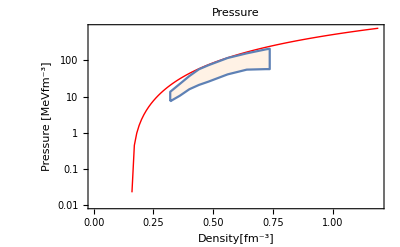

```mathematica
PLTestEoS[[2]]
```

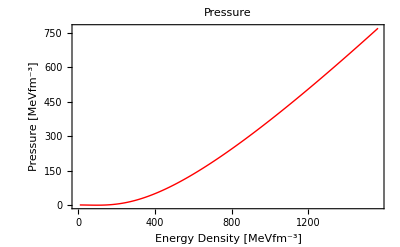

```mathematica
PLTestEoS[[3]]
```

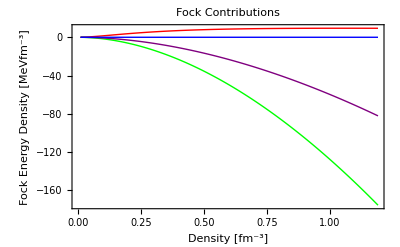

```mathematica
PLTestEoS[[4]]
```

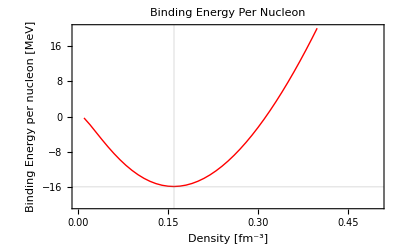

```mathematica
PLTestEoS[[5]]
```

## Functions for just saturation properties

```mathematica
SatProperties[mσType_?StringQ,SMethod_?StringQ,GσL_?NumericQ,GωL_?NumericQ,GρL_?NumericQ,ΛσGeV_,ΛωGeV_,ΛρGeV_,ΛπGeV_]:= Module[{SatData,GσSol,GωSol,GρSol,gσSol,gωSol,gρSol,σ0Sol,mσSol,MStarSol,ϵσHSol,ϵωHSol,ϵρHSol,ϵσF0Sol,ϵωF0Sol,ϵρF0Sol,ϵπF0Sol,K0Sol,L0Sol,coupL,ϵ0Sol,ϵB0Sol,CHECK},

(* OUTPUT: 1,2,3 are the chosen ρ0, BE0, S0 above *)

(* Use input couplings as initial guess and solve for couplings*)
Switch[SMethod,
"Difference",coupL =Couplings[mσType,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];,
"Numerical",coupL =Couplings2[mσType,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];,
_,(* Error only two options Numerical or Difference. Default method will be used, i.e., Numerical *)
 coupL =Couplings2[mσType,GσL,GωL,GρL,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];];

(* OUTPUT: 4,5,6 *)
GσSol = coupL[[1]];
GωSol =coupL[[2]];
GρSol=coupL[[3]];

(* OUTPUT: 7,8,9 *)
gσSol = √(GσSol mσ^2);
gωSol = √(GωSol mω^2);
gρSol = √(GρSol mρ^2);

(* OUTPUT: 10 *)
(* mean sigma field *)
σ0Sol = FSigma[ρ0/2,ρ0/2,mσType,GσSol,ΛσGeV]hbc;

(* OUTPUT: 11 *)
(* effective sigma mass appear in the sigma Fock term *)
mσSol = Effmσ[mσType,ρ0/2,ρ0/2,GσSol,ΛσGeV]hbc;

(* OUTPUT: 12 *)
(* Effective nucleon mass *)
MStarSol =MNS[σ0Sol/hbc,GσSol] hbc;

(* OUTPUT: 13 *)
(* Incompressibility *)
K0Sol = Incompressibility[ρ0,mσType,GσSol,GωSol,GρSol,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];

(* OUTPUT: 14 *)
(* Slope of the symmetry energy *)
Switch[SMethod,"Difference",
L0Sol=Slope[SymEnDifference,ρ0,mσType,GσSol,GωSol,GρSol,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];,"Numerical",L0Sol=Slope[SymEnNUMERICAL,ρ0,mσType,GσSol,GωSol,GρSol,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];,
_,(* Error only two options Numerical or Difference. Default method will be used, i.e., Numerical *)L0Sol=Slope[SymEnNUMERICAL,ρ0,mσType,GσSol,GωSol,GρSol,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV];];

(* OUTPUT:  15 *)
(* Total energy density *)
ϵ0Sol = ϵTotal[ρ0/2,ρ0/2,mσType,GσSol,GωSol,GρSol,ΛσGeV,ΛωGeV,ΛρGeV,ΛπGeV]hbc;

(* OUTPUT:  16 *)
(* Baryon contribution *)
ϵB0Sol =ϵB[ρ0/2,ρ0/2,σ0Sol/hbc,GσSol]hbc;

(* OUTPUT:  17,18,19 *)
(* Hartree contributions to the energy density *)
ϵσHSol =ϵσH[σ0Sol/hbc]hbc;
ϵωHSol =ϵωH[ρ0/2,ρ0/2,GωSol]hbc;
ϵρHSol =ϵρH[ρ0/2,ρ0/2,GρSol]hbc;

(* OUTPUT:  20,21,22,23 *)
(* Fock contributions to the energy density *)
ϵσF0Sol =ϵσF[ρ0/2,ρ0/2,σ0Sol/hbc,Effmσ[mσType,ρ0/2,ρ0/2,GσSol,ΛσGeV],GσSol,ΛσGeV]hbc;
ϵωF0Sol =ϵωF[ρ0/2,ρ0/2,GωSol,ΛωGeV]hbc;
ϵρF0Sol =ϵρF[ρ0/2,ρ0/2,GρSol,ΛρGeV] hbc;
ϵπF0Sol =ϵπF[ρ0/2,ρ0/2,ΛπGeV] hbc;


(* OUTPUT:  24 *)
(* check that the sum of each component is the same as the total *)
CHECK =ϵ0Sol - (ϵB0Sol +ϵσHSol+ϵωHSol+ϵρHSol+ϵσF0Sol+ϵωF0Sol +ϵρF0Sol+ϵπF0Sol);

SatData = {ρ0,BE0 hbc,S0 hbc,GσSol,GωSol,GρSol,gσSol,gωSol,gρSol,σ0Sol,mσSol,MStarSol,K0Sol,L0Sol,ϵ0Sol ,ϵB0Sol ,ϵσHSol,ϵωHSol,ϵρHSol,ϵσF0Sol,ϵωF0Sol ,ϵρF0Sol,ϵπF0Sol,CHECK};

Return[SatData];
];
```

```mathematica
Test =SatProperties["Effρv","Difference",Gσ,Gω,Gρ,∞,∞,∞,0]//AbsoluteTiming
```

{4.59906,{0.16,-15.865,30.,11.33805361130194,7.200608927933539,4.241229618643045,11.94484897728764,10.64235706415205,8.096718459288483,22.800444107163,789.714803679718,694.910305633429,340.5362225731111,53.01854839285486,147.7016,115.848970219626,16.5764988236381,18.1871992262991,0.,2.89230214971062,-4.02757227942161,-1.77579813985228,0,0.}}

```mathematica
Test =SatProperties["Effρv","Numerical",Gσ,Gω,Gρ,∞,∞,∞,0]//AbsoluteTiming
```

{7.08899,{0.16,-15.865,30.,11.31775456414725,7.24551973073528,4.518551832808334,11.93415147645819,10.67549411236348,8.357238178385703,22.7890964144231,789.56329211652,695.21097595547,340.4179724113179,53.27027307583741,147.7016,115.895155731237,16.5600028111129,18.3006343157676,0.,2.89041237147121,-4.05269258608195,-1.891912643507,0,0.}}

```mathematica
Test =SatProperties["Effρv","Numerical",Gσ,Gω,Gρ,0.9`20,0.9`20,0.9`20,0.9`20]//AbsoluteTiming
```

{262.588,{0.16,-15.865,30.,9.434207297329365,5.675867715816332,3.006236179401435,10.89592530779642,9.448640952874506,6.816708045838096,21.6046221325413,775.375727837001,724.709080122473,319.2543705703259,67.87000967741343,147.7016,120.433556866453,14.8833105710198,14.3360287946224,0.,1.91624226754088,-2.26204186993471,-0.89707396505242,-0.708422664649193,0.}}

Functions to extract specific quantities for later tables

```mathematica
ExtractCCData[mylist_?ListQ,ModelName_?StringQ]:=N[Join[{ModelName},Part[mylist,2;;3],{mylist[[1]]},Part[mylist,4;;9]],5];
```

```mathematica
ExtractNMSatData[mylist_?ListQ,ModelName_?StringQ]:= N[Join[{ModelName},Part[mylist,2;;3],{mylist[[1]]},Part[mylist,10;;14]],5];
```

```mathematica
ExtractFockEnDen[mylist_?ListQ,ModelName_?StringQ]:= N[Join[{ModelName},Part[mylist,2;;3],{mylist[[1]]},Part[mylist,20;;23]],5];
```

## Actual Calculations for model variations

### 1. "MyQMC700Diff" - (m^*)_σ changes with total baryonic density (Keep Default RED)

```mathematica
sol1 =SatProperties["Effρv","Difference",Gσ,Gω,Gρ,∞,∞,∞,0]//AbsoluteTiming
```

{4.30491,{0.16,-15.865,30.,11.33805361130194,7.200608927933539,4.241229618643045,11.94484897728764,10.64235706415205,8.096718459288483,22.800444107163,789.714803679718,694.910305633429,340.5362225731111,53.01854839285486,147.7016,115.848970219626,16.5764988236381,18.1871992262991,0.,2.89230214971062,-4.02757227942161,-1.77579813985228,0,0.}}

Extract data for tables below

```mathematica
MyQMC700DiffOnlyCC=ExtractCCData[sol1[[2]],"MyQMC700Diff"];
MyQMC700DiffNMSat = ExtractNMSatData[sol1[[2]],"MyQMC700Diff"];
MyQMC700DiffFockEnDen = ExtractFockEnDen[sol1[[2]],"MyQMC700Diff"];
```

Make EoS table

```mathematica
sol1Data =EoSTable["Effρv",sol1[[2,4]],sol1[[2,5]],sol1[[2,6]],∞,∞,∞,0,0.01`20,1.2`20,0.01`20,"QMC700_Effrv_Diff"]//AbsoluteTiming;
```

Make plots (remove semi-colon to show)

```mathematica
PLsol1EoS=PlotEoS[sol1Data[[2]]];
```

```mathematica
PLsol1EoS[[1]];
```

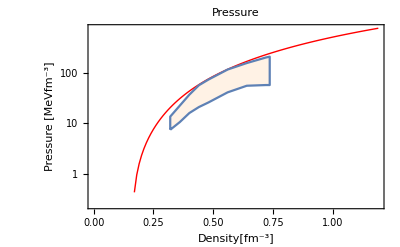

```mathematica
PLsol1EoS[[2]]
```

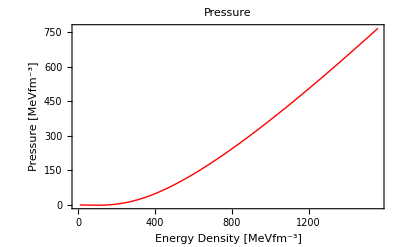

```mathematica
PLsol1EoS[[3]]
```

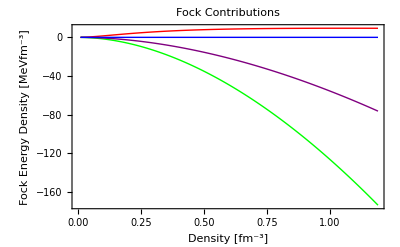

```mathematica
PLsol1EoS[[4]]
```

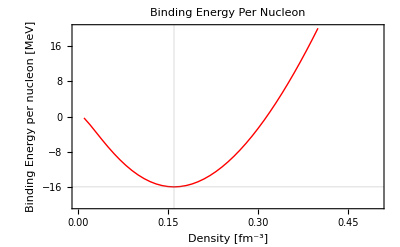

```mathematica
PLsol1EoS[[5]]
```

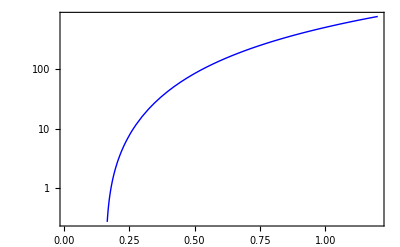

```mathematica
PressSol1=LogPlot[PressureSNM[ρ,"Effρv",sol1[[2,4]],sol1[[2,5]],sol1[[2,6]],∞,∞,∞,0],{ρ,0.01`20,1.2`20},PlotStyle->{Thick,Blue},Frame-> True]
```

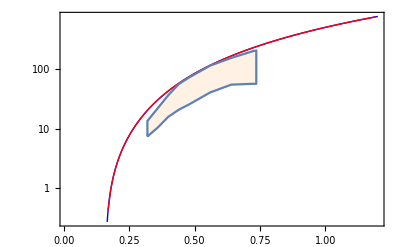

```mathematica
mysol1plot=Show[PressSol1,PLsol1EoS[[2]]]
```

How to change colour of calculated plot

```mathematica
newPressSol1=restylePlot[PressSol1,{{Thick,Green}},Frame->True];
```

How to change colour of plot from data file

```mathematica
newPLsol1EoS=restylePlot[PLsol1EoS[[2]],{{Thick,Green},{Black}}];
```

### 2. "MyQMC700FREEDiff" - (m^*)_σ =m_σ (Default RED -> BLUE)

```mathematica
sol2 =SatProperties["FREE","Difference",Gσ,Gω,Gρ,∞,∞,∞,0]//AbsoluteTiming
```

{5.04093,{0.16,-15.865,30.,11.21155931620009,6.55819591832414,3.251120613479643,11.8780300477077,10.15653119888609,7.088913649176122,22.7292815470474,700.,696.789659237563,315.444397422387,52.63077098667292,147.7016,116.137680208728,16.4731863424798,16.564601261562,0.,3.55561922666341,-3.6682464424906,-1.36124059694266,0,0.}}

Extract data for tables below

```mathematica
MyQMC700FREEDiffOnlyCC=ExtractCCData[sol2[[2]],"MyQMC700FREEDiff"];
MyQMC700FREEDiffNMSat = ExtractNMSatData[sol2[[2]],"MyQMC700FREEDiff"];
MyQMC700FREEDiffFockEnDen = ExtractFockEnDen[sol2[[2]],"MyQMC700FREEDiff"];
```

Make EoS table

```mathematica
sol2Data =EoSTable["FREE",sol2[[2,4]],sol2[[2,5]],sol2[[2,6]],∞,∞,∞,0,0.01`20,1.2`20,0.01`20,"QMC700_FREE_Diff"]//AbsoluteTiming;
```

Make plots (remove semi-colon to show)

```mathematica
PLsol2EoS=PlotEoS[sol2Data[[2]]];
```

```mathematica
PLsol2EoS[[1]];
```

```mathematica
PLsol2EoS[[2]];
```

```mathematica
PLsol2EoS[[3]];
```

```mathematica
PLsol2EoS[[4]];
```

```mathematica
PLsol2EoS[[5]];
```

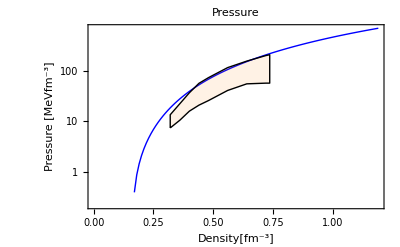

```mathematica
newPLsol2EoS=restylePlot[PLsol2EoS[[2]],{{Thick,Blue},{Black}}]
```

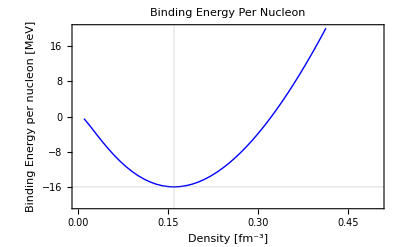

```mathematica
newPLsol2EoS5=restylePlot[PLsol2EoS[[5]],{{Thick,Blue}}]
```

### 3. "MyQMC700Num" - (m^*)_σ changes with total baryonic density (Default RED -> GREEN)

```mathematica
sol3 =SatProperties["Effρv","Numerical",Gσ,Gω,Gρ,∞,∞,∞,0]//AbsoluteTiming
```

{7.10103,{0.16,-15.865,30.,11.31775456414725,7.24551973073528,4.518551832808334,11.93415147645819,10.67549411236348,8.357238178385703,22.7890964144231,789.56329211652,695.21097595547,340.4179724113179,53.27027307583741,147.7016,115.895155731237,16.5600028111129,18.3006343157676,0.,2.89041237147121,-4.05269258608195,-1.891912643507,0,0.}}

Extract data for tables below

```mathematica
MyQMC700NumOnlyCC=ExtractCCData[sol3[[2]],"MyQMC700Num"];
MyQMC700NumNMSat = ExtractNMSatData[sol3[[2]],"MyQMC700Num"];
MyQMC700NumFockEnDen = ExtractFockEnDen[sol3[[2]],"MyQMC700Num"];
```

Make EoS table

```mathematica
sol3Data =EoSTable["Effρv",sol3[[2,4]],sol3[[2,5]],sol3[[2,6]],∞,∞,∞,0,0.01`20,1.2`20,0.01`20,"QMC700_Effrv_Num"]//AbsoluteTiming;
```

Make plots (remove semi-colon to show)

```mathematica
PLsol3EoS=PlotEoS[sol3Data[[2]]];
```

```mathematica
PLsol3EoS[[1]];
```

```mathematica
PLsol3EoS[[2]];
```

```mathematica
PLsol3EoS[[3]];
```

```mathematica
PLsol3EoS[[4]];
```

```mathematica
PLsol3EoS[[5]];
```

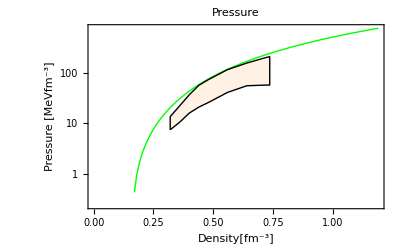

```mathematica
newPLsol3EoS2=restylePlot[PLsol3EoS[[2]],{{Thick,Green},{Black}}]
```

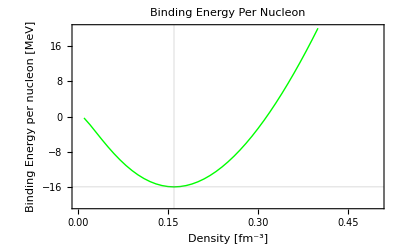

```mathematica
newPLsol3EoS5=restylePlot[PLsol3EoS[[5]],{{Thick,Green}}]
```

### 4. "MyQMC700FREENum" - (m^*)_σ =m_σ (PINK)

```mathematica
sol4 =SatProperties["FREE","Numerical",Gσ,Gω,Gρ,∞,∞,∞,0]//AbsoluteTiming
```

{7.21021,{0.16,-15.865,30.,11.18778057965535,6.609178785159162,3.563957828501754,11.86542723046016,10.19593278323003,7.422144812983398,22.7157840173738,700.,697.144470487632,315.3910344534177,52.41321414891272,147.7016,116.192193761521,16.4536273166671,16.6933730870474,0.,3.55139411053869,-3.69676308368654,-1.49222519208716,0,0.}}

Extract data for tables below

```mathematica
MyQMC700FREENumOnlyCC=ExtractCCData[sol4[[2]],"MyQMC700FREENum"];
MyQMC700FREENumNMSat = ExtractNMSatData[sol4[[2]],"MyQMC700FREENum"];
MyQMC700FREENumFockEnDen = ExtractFockEnDen[sol4[[2]],"MyQMC700FREENum"];
```

Make EoS table

```mathematica
sol4Data =EoSTable["FREE",sol4[[2,4]],sol4[[2,5]],sol4[[2,6]],∞,∞,∞,0,0.01`20,1.2`20,0.01`20,"QMC700_FREE_Num"]//AbsoluteTiming;
```

Make plots (remove semi-colon to show)

```mathematica
PLsol4EoS=PlotEoS[sol4Data[[2]]];
```

```mathematica
PLsol4EoS[[1]];
```

```mathematica
PLsol4EoS[[2]];
```

```mathematica
PLsol4EoS[[3]];
```

```mathematica
PLsol4EoS[[4]];
```

```mathematica
PLsol4EoS[[5]];
```

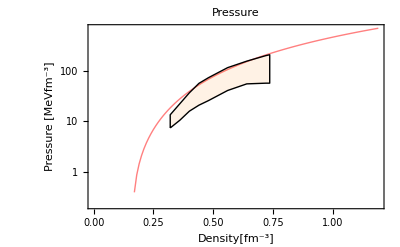

```mathematica
newPLsol4EoS2=restylePlot[PLsol4EoS[[2]],{{Thick,Pink},{Black}}]
```

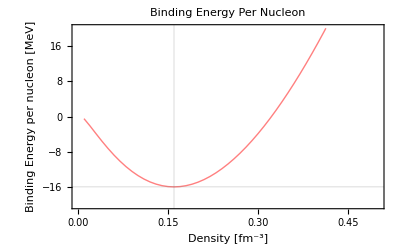

```mathematica
newPLsol4EoS5=restylePlot[PLsol4EoS[[5]],{{Thick,Pink}}]
```

### 5. "MyQMC700πNum" - (m^*)_σ changes with total baryonic density (Orange)

```mathematica
sol5 =SatProperties["Effρv","Numerical",Gσ,Gω,Gρ,∞,∞,∞,∞]//AbsoluteTiming
```

{14.2372,{0.16,-15.865,30.,10.62583848252372,7.085894329234268,3.918762772014398,11.56359879447587,10.55724376323773,7.782831574843669,22.3853333335,784.381348180079,705.672540942238,320.7682777128249,52.13812164266653,147.7016,117.503091277066,15.9784013629134,17.8974546669723,0.,2.82180576450303,-3.9634080757563,-1.64078162862873,-0.894963367069797,0.}}

Extract data for tables below

```mathematica
MyQMC700πNumOnlyCC=ExtractCCData[sol5[[2]],"MyQMC700πNum"];
MyQMC700πNumNMSat = ExtractNMSatData[sol5[[2]],"MyQMC700πNum"];
MyQMC700πNumFockEnDen = ExtractFockEnDen[sol5[[2]],"MyQMC700πNum"];
```

Make EoS table

```mathematica
sol5Data =EoSTable["Effρv",sol5[[2,4]],sol5[[2,5]],sol5[[2,6]],∞,∞,∞,∞,0.01`20,1.2`20,0.01`20,"QMC700pi_Num"]//AbsoluteTiming;
```

Make plots (remove semi-colon to show)

```mathematica
PLsol5EoS=PlotEoS[sol5Data[[2]]];
```

```mathematica
PLsol5EoS[[1]];
```

```mathematica
PLsol5EoS[[2]];
```

```mathematica
PLsol5EoS[[3]];
```

```mathematica
PLsol5EoS[[4]];
```

```mathematica
PLsol5EoS[[5]];
```

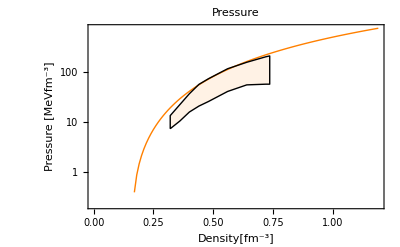

```mathematica
newPLsol5EoS2=restylePlot[PLsol5EoS[[2]],{{Thick,Orange},{Black}}]
```

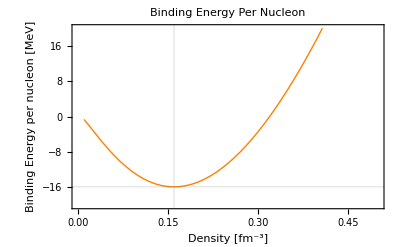

```mathematica
newPLsol5EoS5=restylePlot[PLsol5EoS[[5]],{{Thick,Orange}}]
```

### 6. "MyQMC700πFREENum" - (m^*)_σ=m_σ (Brown) --NEEDS WP = 16

```mathematica
sol6 =SatProperties["FREE","Numerical",Gσ,Gω,Gρ,∞,∞,∞,∞]//AbsoluteTiming
```

{13.6526,{0.16,-15.865,30.,10.46565570083605,6.471514794490911,3.03545679045116,11.47610813280785,10.08918737618769,6.849757126664645,22.2869490840514,700.,708.1547726004,298.1382404812556,51.71133761793288,147.7016,117.884875224766,15.8382588457929,16.3456632683877,0.,3.41847084055648,-3.6197624191262,-1.27094239330757,-0.894963367069797,0.}}

Extract data for tables below

```mathematica
MyQMC700πFREENumOnlyCC=ExtractCCData[sol6[[2]],"MyQMC700πFREENum"];
MyQMC700πFREENumNMSat = ExtractNMSatData[sol6[[2]],"MyQMC700πFREENum"];
MyQMC700πFREENumFockEnDen = ExtractFockEnDen[sol6[[2]],"MyQMC700πFREENum"];
```

Make EoS table

```mathematica
sol6Data =EoSTable["FREE",sol6[[2,4]],sol6[[2,5]],sol6[[2,6]],∞,∞,∞,∞,0.01`20,1.2`20,0.01`20,"QMC700pi_FREE_Num"]//AbsoluteTiming;
```

Make plots (remove semi-colon to show)

```mathematica
PLsol6EoS=PlotEoS[sol6Data[[2]]];
```

```mathematica
PLsol6EoS[[1]];
```

```mathematica
PLsol6EoS[[2]];
```

```mathematica
PLsol6EoS[[3]];
```

```mathematica
PLsol6EoS[[4]];
```

```mathematica
PLsol6EoS[[5]];
```

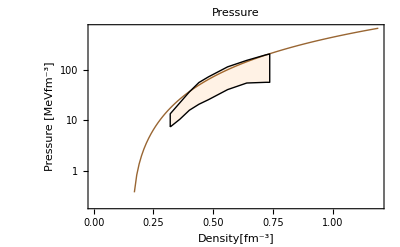

```mathematica
newPLsol6EoS2=restylePlot[PLsol6EoS[[2]],{{Thick,Brown},{Black}}]
```

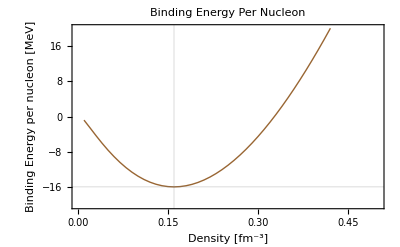

```mathematica
newPLsol6EoS5=restylePlot[PLsol6EoS[[5]],{{Thick,Brown}}]
```

Return WP to Machine precision

```mathematica
(*WP=MachinePrecision;*)
```

### 7. "MyQMC700πΛ900Num" - (m^*)_σ changes with total baryonic density (Purple)

```mathematica
sol7 =SatProperties["Effρv","Numerical",Gσ,Gω,Gρ,0.9`20,0.9`20,0.9`20,0.9`20]//AbsoluteTiming
```

{271.942,{0.16,-15.865,30.,9.434207297329365,5.675867715816332,3.006236179401435,10.89592530779642,9.448640952874506,6.816708045838096,21.6046221325413,775.375727837001,724.709080122473,319.2543705703259,67.87000967741343,147.7016,120.433556866453,14.8833105710198,14.3360287946224,0.,1.91624226754088,-2.26204186993471,-0.89707396505242,-0.708422664649193,0.}}

Extract data for tables below

```mathematica
MyQMC700πΛ900NumOnlyCC=ExtractCCData[sol7[[2]],"MyQMC700πΛ900Num"];
MyQMC700πΛ900NumNMSat = ExtractNMSatData[sol7[[2]],"MyQMC700πΛ900Num"];
MyQMC700πΛ900NumFockEnDen = ExtractFockEnDen[sol7[[2]],"MyQMC700πΛ900Num"];
```

Make EoS table

```mathematica
sol7Data =EoSTable["Effρv",sol7[[2,4]],sol7[[2,5]],sol7[[2,6]],0.9`20,0.9`20,0.9`20,0.9`20,0.01`20,1.2`20,0.01`20,"QMC700piL900_Num"]//AbsoluteTiming;
```

Make plots (remove semi-colon to show)

```mathematica
PLsol7EoS=PlotEoS[sol7Data[[2]]];
```

```mathematica
PLsol7EoS[[1]];
```

```mathematica
PLsol7EoS[[2]];
```

```mathematica
PLsol7EoS[[3]];
```

```mathematica
PLsol7EoS[[4]];
```

```mathematica
PLsol7EoS[[5]];
```

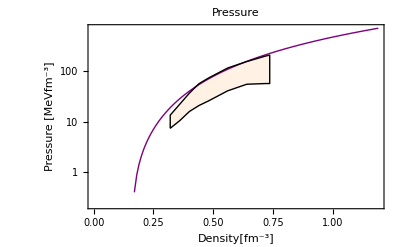

```mathematica
newPLsol7EoS2=restylePlot[PLsol7EoS[[2]],{{Thick,Purple},{Black}}]
```

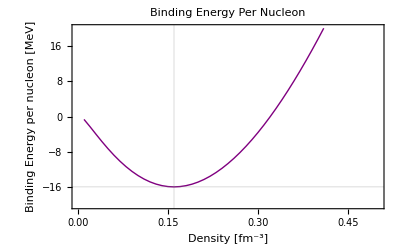

```mathematica
newPLsol7EoS5=restylePlot[PLsol7EoS[[5]],{{Thick,Purple}}]
```

### 8. "MyQMC700πΛ900FREENum" - (m^*)_σ=m_σ (Black) (Need WP = 16)

```mathematica
sol8 =SatProperties["FREE","Numerical",Gσ,Gω,Gρ,0.9`20,0.9`20,0.9`20,0.9`20]//AbsoluteTiming
```

{273.946,{0.16,-15.865,30.,9.451123870563104,5.46556195520075,2.717306839003287,10.90568972993181,9.271940253561743,6.48085770735751,21.616538907111,700.,724.429355613773,306.0157433241418,66.19082384741839,147.7016,120.390455303186,14.8997339058639,13.8048413901911,0.,2.30407555299335,-2.17822729570225,-0.810856191882464,-0.708422664649193,0.}}

Extract data for tables below

```mathematica
MyQMC700πΛ900FREENumOnlyCC=ExtractCCData[sol8[[2]],"MyQMC700πΛ900FREENum"];
MyQMC700πΛ900FREENumNMSat = ExtractNMSatData[sol8[[2]],"MyQMC700πΛ900FREENum"];
MyQMC700πΛ900FREENumFockEnDen = ExtractFockEnDen[sol8[[2]],"MyQMC700πΛ900FREENum"];
```

Make EoS table

```mathematica
sol8Data =EoSTable["FREE",sol8[[2,4]],sol8[[2,5]],sol8[[2,6]],0.9`20,0.9`20,0.9`20,0.9`20,0.01`20,1.2`20,0.01`20,"QMC700piL900_FREE_Num"]//AbsoluteTiming;
```

Make plots (remove semi-colon to show)

```mathematica
PLsol8EoS=PlotEoS[sol8Data[[2]]];
```

```mathematica
PLsol8EoS[[1]];
```

```mathematica
PLsol8EoS[[2]];
```

```mathematica
PLsol8EoS[[3]];
```

```mathematica
PLsol8EoS[[4]];
```

```mathematica
PLsol8EoS[[5]];
```

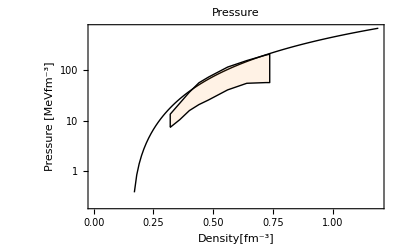

```mathematica
newPLsol8EoS2=restylePlot[PLsol8EoS[[2]],{{Thick,Black},{Black}}]
```

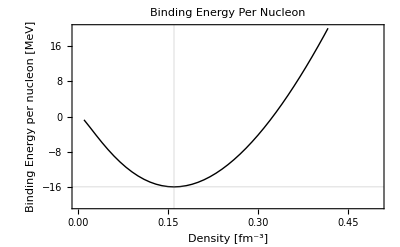

```mathematica
newPLsol8EoS5=restylePlot[PLsol8EoS[[5]],{{Thick,Black}}]
```

### 9. "MyQMC700πΛ1300Num" - (m^*)_σ changes with total baryonic density (Yellow)

```mathematica
sol9 =SatProperties["Effρv","Numerical",Gσ,Gω,Gρ,1.3`20,1.3`20,1.3`20,1.3`20]//AbsoluteTiming
```

{284.909,{0.16,-15.865,30.,9.861100812964657,6.168312542039667,3.228713895640835,11.13971575759412,9.850003823312526,7.064443022883287,21.8976961802374,778.61390182795,717.73534597018,322.2540599403058,63.09901332004918,147.7016,119.359363418255,15.2898437152399,15.5798391795664,0.,2.3018195688122,-2.89915529873721,-1.136107554994,-0.794003028142186,0.}}

Extract data for tables below

```mathematica
MyQMC700πΛ1300NumOnlyCC=ExtractCCData[sol9[[2]],"MyQMC700πΛ1300Num"];
MyQMC700πΛ1300NumNMSat = ExtractNMSatData[sol9[[2]],"MyQMC700πΛ1300Num"];
MyQMC700πΛ1300NumFockEnDen = ExtractFockEnDen[sol9[[2]],"MyQMC700πΛ1300Num"];
```

Make EoS table

```mathematica
sol9Data =EoSTable["Effρv",sol9[[2,4]],sol9[[2,5]],sol9[[2,6]],1.3`20,1.3`20,1.3`20,1.3`20,0.01`20,1.2`20,0.01`20,"QMC700piL1300_Num"]//AbsoluteTiming;
```

Make plots (remove semi-colon to show)

```mathematica
PLsol9EoS=PlotEoS[sol9Data[[2]]];
```

```mathematica
PLsol9EoS[[1]];
```

```mathematica
PLsol9EoS[[2]];
```

```mathematica
PLsol9EoS[[3]];
```

```mathematica
PLsol9EoS[[4]];
```

```mathematica
PLsol9EoS[[5]];
```

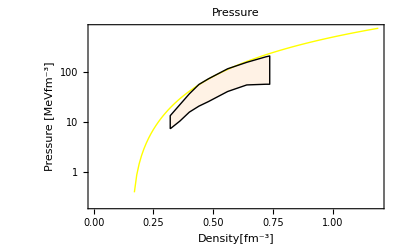

```mathematica
newPLsol9EoS2=restylePlot[PLsol9EoS[[2]],{{Thick,Yellow},{Black}}]
```

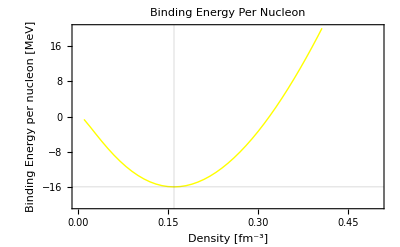

```mathematica
newPLsol9EoS5=restylePlot[PLsol9EoS[[5]],{{Thick,Yellow}}]
```

### 10. "MyQMC700πΛ1300FREENum" - (m^*)_σ=m_σ (Gray)

```mathematica
sol10 =SatProperties["FREE","Numerical",Gσ,Gω,Gρ,1.3`20,1.3`20,1.3`20,1.3`20]//AbsoluteTiming
```

{258.643,{0.16,-15.865,30.,9.830364466651464,5.833930539893209,2.758180043970224,11.12234135949175,9.579301458975809,6.529417686804789,21.8771158990947,700.,718.231588650895,305.0836664666265,61.40699623666676,147.7016,119.43577679307,15.261117276562,14.735261706801,0.,2.77597827990454,-2.74199313376613,-0.970537894428798,-0.794003028142186,0.}}

Extract data for tables below

```mathematica
MyQMC700πΛ1300FREENumOnlyCC=ExtractCCData[sol10[[2]],"MyQMC700πΛ1300FREENum"];
MyQMC700πΛ1300FREENumNMSat = ExtractNMSatData[sol10[[2]],"MyQMC700πΛ1300FREENum"];
MyQMC700πΛ1300FREENumFockEnDen = ExtractFockEnDen[sol10[[2]],"MyQMC700πΛ1300FREENum"];
```

Make EoS table

```mathematica
sol10Data =EoSTable["FREE",sol10[[2,4]],sol10[[2,5]],sol10[[2,6]],1.3`20,1.3`20,1.3`20,1.3`20,0.01`20,1.2`20,0.01`20,"QMC700piL1300_FREE_Num"]//AbsoluteTiming;
```

Make plots (remove semi-colon to show)

```mathematica
PLsol10EoS=PlotEoS[sol10Data[[2]]];
```

```mathematica
PLsol10EoS[[1]];
```

```mathematica
PLsol10EoS[[2]];
```

```mathematica
PLsol10EoS[[3]];
```

```mathematica
PLsol10EoS[[4]];
```

```mathematica
PLsol10EoS[[5]];
```

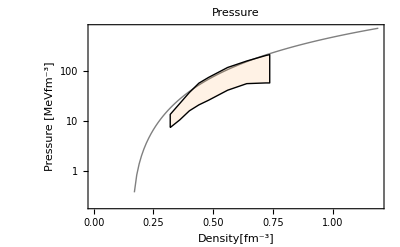

```mathematica
newPLsol10EoS2=restylePlot[PLsol10EoS[[2]],{{Thick,Gray},{Black}}]
```

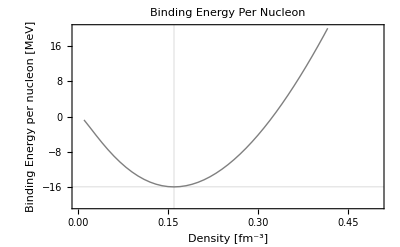

```mathematica
newPLsol10EoS5=restylePlot[PLsol10EoS[[5]],{{Thick,Gray}}]
```

### 11. "MyQMC700πΛσInfΛωρπ900FREENum" - (m^*)_σ=m_σ (Dark Green)

```mathematica
sol11 =SatProperties["FREE","Numerical",Gσ,Gω,Gρ,∞,0.9`20,0.9`20,0.9`20]//AbsoluteTiming
```

{239.345,{0.16,-15.865,30.,9.974736454863437,5.090730506354794,0.7220112308503646,11.20371686595506,8.948356276712872,3.340681883212757,21.973102273934,700.,715.908473447162,286.8685684457097,56.78642799132852,147.7016,119.078087821032,15.3953281006022,12.8580972599832,0.,3.32280396642311,-2.02884318847665,-0.215451294914652,-0.708422664649193,0.}}

Extract data for tables below

```mathematica
MyQMC700πΛσInfΛωρπ900FREENumOnlyCC=ExtractCCData[sol11[[2]],"MyQMC700πΛσInfΛωρπ900FREENum"];
MyQMC700πΛσInfΛωρπ900FREENumNMSat = ExtractNMSatData[sol11[[2]],"MyQMC700πΛσInfΛωρπ900FREENum"];
MyQMC700πΛσInfΛωρπ900FREENumFockEnDen = ExtractFockEnDen[sol11[[2]],"MyQMC700πΛσInfΛωρπ900FREENum"];
```

Make EoS table

```mathematica
sol11Data =EoSTable["FREE",sol11[[2,4]],sol11[[2,5]],sol11[[2,6]],∞,0.9`20,0.9`20,0.9`20,0.01`20,1.2`20,0.01`20,"QMC700piLsInfLwrp900_FREE_Num"]//AbsoluteTiming;
```

Make plots (remove semi-colon to show)

```mathematica
PLsol11EoS=PlotEoS[sol11Data[[2]]];
```

```mathematica
PLsol11EoS[[1]];
```

```mathematica
PLsol11EoS[[2]];
```

```mathematica
PLsol11EoS[[3]];
```

```mathematica
PLsol11EoS[[4]];
```

```mathematica
PLsol11EoS[[5]];
```

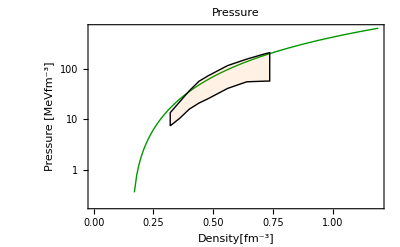

```mathematica
newPLsol11EoS2=restylePlot[PLsol11EoS[[2]],{{Thick,Darker[Green,0.4]},{Black}}]
```

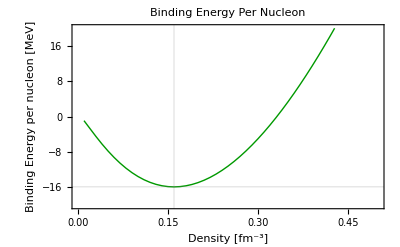

```mathematica
newPLsol11EoS5=restylePlot[PLsol11EoS[[5]],{{Thick,Darker[Green,0.4]}}]
```

## Test against my Fortran code (Hartree Scenario)

Hartree calculation with my rounded off couplings. Note that the symmetry energy in this case was different. It was taken to be 32.5MeV, also RNFREE =1fm.

```mathematica
RNFREE =1;
S0 = 32.5`20/hbc;
```

Note that saturation occurs where it should

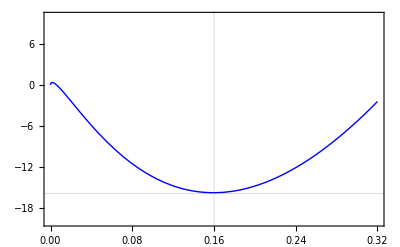

```mathematica
Plot[{BindingEnergy[ρ,"Effρv",(10.25`20)^2/mσ^2,(7.95`20)^2/mω^2,(8.40`20)^2/mρ^2,0,0,0,0]hbc} ,{ρ,0,2 ρ0},PlotRange->{-20,10},PlotStyle-> {{Thick,Blue}},GridLines->{{ρ0},{BE0 hbc}},Frame->True]
```

For Hartree SatProperties complains if MachinePrecision is used. It does not find correct couplings unless WP =16. Once increased it does give the correct couplings, K_0 and L_0. My Hartree RNFREE =1 fm and S0 = 32.5 MeV

```mathematica
Test1 =SatProperties["Effρv","NUMERICAL",Gσ,Gω,Gρ,0,0,0,0]//AbsoluteTiming
```

{0.57742,{0.16,-15.865,32.5,8.35347611338251,4.012794248167196,4.566248198533778,10.25286000934654,7.944684585102916,8.401230536953512,20.1607450760596,779.545836130904,751.750506204799,283.2941316620206,88.21390325254161,147.7016,124.605711133691,12.9604282162463,10.1354606500631,0.,0,0,0,0,0.}}

```mathematica
Slope[SymEnNUMERICAL,ρ0,"Effρv",(10.25`20)^2/mσ^2,(7.95`20)^2/mω^2,(8.40`20)^2/mρ^2,0,0,0,0]
```

88.19322692069221

```mathematica
Slope[SymEnNUMERICAL,ρ0,"Effρv",Test1[[2,7]]^2/mσ^2,Test1[[2,8]]^2/mω^2,Test1[[2,9]]^2/mρ^2,0,0,0,0]
```

88.21390325254161

```mathematica
S0 =30/hbc;
RNFREE=0.8`20;
```

## Summary tables of the above calculations

Three tables are produced for easy comparison of model variations from the scenarios calucated above.

Headings and units for tables

```mathematica
CCOnlyTableHeadings ={"Model","B. En.^*","S_0^*","ρ_0^*","G_σ","G_ω","G_ρ","g_σ","g_ω","g_ρ"};
CCOnlyTableUnits = {"", "[MeV]","[MeV]","[fm^-3]","[fm^-2]","[fm^-2]","[fm^-2]"," "," "," "};
```

```mathematica
NMSatTableHeadings={"Model","B. En.^*","S_0^*","ρ_0^*","σ_0","(m^*)_σ","(M^*)_N","K_0","L_0"};
```

```mathematica
NMSatTableUnits = {"", "[MeV]","[MeV]","[fm^-3]","[MeV]","[MeV]","[MeV]","[MeV]","[MeV]"};
```

```mathematica
FockEnDenTableHeadings={"Model","B. En.^*","S_0^*","ρ_0^*","(SuperscriptBox[ϵ, F])_σ","(ϵ^F)_ω","(ϵ^F)_ρ","(ϵ^F)_π"};
```

```mathematica
FockEnDenTableUnits = {"", "[MeV]","[MeV]","[fm^-3]","[MeVfm^-3]","[MeVfm^-3]","[MeVfm^-3]","[MeVfm^-3]"};
```

### Naming convention of different model variations (a bit long)

MyQMC700 - My version of QMC700 with (m^*)_σ . Only σ, ω, ρ Fock terms included.

π => Pion Fock term included.

Diff => Difference method for symmetry energy used

Num => Numerical finite difference method used for the symmetry energy

Λ### => Form factor included with cut-off ### [MeV] (Note that in calculation it is given to functions  in GeV)

FREE => Free sigma meson mass is used in sigma Fock term.

ΛσInfΛωρπ900 => the sigma meson cut-off is taken to infinity (no form factor), whereas the other mesons have a form factor of 900 MeV.

The best reproduction of QMC700 is MyQMC700Num, but is a little off. The possible differences between my calculation and the papers above are described at the beginning of this notebook.

### Coupling constants

```mathematica
MyDataCCOnly ={CCOnlyTableHeadings,CCOnlyTableUnits,MyQMC700DiffOnlyCC,MyQMC700FREEDiffOnlyCC,MyQMC700NumOnlyCC,MyQMC700FREENumOnlyCC,MyQMC700πNumOnlyCC,MyQMC700πFREENumOnlyCC,MyQMC700πΛ900NumOnlyCC,MyQMC700πΛ900FREENumOnlyCC,MyQMC700πΛ1300NumOnlyCC,MyQMC700πΛ1300FREENumOnlyCC,MyQMC700πΛσInfΛωρπ900FREENumOnlyCC};
```

```mathematica
Grid[MyDataCCOnly,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,LightGray,None}}]
```

Model | B. En.^* | S_0^* | ρ_0^* | G_σ | G_ω | G_ρ | g_σ | g_ω | g_ρ
 | [MeV] | [MeV] | [fm^-3] | [fm^-2] | [fm^-2] | [fm^-2] |   |   |  
MyQMC700Diff | -15.865 | 30. | 0.16 | 11.338 | 7.2006 | 4.2412 | 11.945 | 10.642 | 8.0967
MyQMC700FREEDiff | -15.865 | 30. | 0.16 | 11.212 | 6.5582 | 3.2511 | 11.878 | 10.157 | 7.0889
MyQMC700Num | -15.865 | 30. | 0.16 | 11.318 | 7.2455 | 4.5186 | 11.934 | 10.675 | 8.3572
MyQMC700FREENum | -15.865 | 30. | 0.16 | 11.188 | 6.6092 | 3.564 | 11.865 | 10.196 | 7.4221
MyQMC700πNum | -15.865 | 30. | 0.16 | 10.626 | 7.0859 | 3.9188 | 11.564 | 10.557 | 7.7828
MyQMC700πFREENum | -15.865 | 30. | 0.16 | 10.466 | 6.4715 | 3.0355 | 11.476 | 10.089 | 6.8498
MyQMC700πΛ900Num | -15.865 | 30. | 0.16 | 9.4342 | 5.6759 | 3.0062 | 10.896 | 9.4486 | 6.8167
MyQMC700πΛ900FREENum | -15.865 | 30. | 0.16 | 9.4511 | 5.4656 | 2.7173 | 10.906 | 9.2719 | 6.4809
MyQMC700πΛ1300Num | -15.865 | 30. | 0.16 | 9.8611 | 6.1683 | 3.2287 | 11.14 | 9.85 | 7.0644
MyQMC700πΛ1300FREENum | -15.865 | 30. | 0.16 | 9.8304 | 5.8339 | 2.7582 | 11.122 | 9.5793 | 6.5294
MyQMC700πΛσInfΛωρπ900FREENum | -15.865 | 30. | 0.16 | 9.9747 | 5.0907 | 0.72201 | 11.204 | 8.9484 | 3.3407

### Nuclear matter properties at saturation density

```mathematica
MyDataNMSat={NMSatTableHeadings,NMSatTableUnits,MyQMC700DiffNMSat,MyQMC700FREEDiffNMSat,MyQMC700NumNMSat,MyQMC700FREENumNMSat,MyQMC700πNumNMSat,MyQMC700πFREENumNMSat,MyQMC700πΛ900NumNMSat,MyQMC700πΛ900FREENumNMSat,MyQMC700πΛ1300NumNMSat,MyQMC700πΛ1300FREENumNMSat,MyQMC700πΛσInfΛωρπ900FREENumNMSat};
```

```mathematica
Grid[MyDataNMSat,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,LightGray,None}}]
```

Model | B. En.^* | S_0^* | ρ_0^* | σ_0 | (m^*)_σ | (M^*)_N | K_0 | L_0
 | [MeV] | [MeV] | [fm^-3] | [MeV] | [MeV] | [MeV] | [MeV] | [MeV]
MyQMC700Diff | -15.865 | 30. | 0.16 | 22.8 | 789.71 | 694.91 | 340.54 | 53.019
MyQMC700FREEDiff | -15.865 | 30. | 0.16 | 22.729 | 700. | 696.79 | 315.44 | 52.631
MyQMC700Num | -15.865 | 30. | 0.16 | 22.789 | 789.56 | 695.21 | 340.42 | 53.27
MyQMC700FREENum | -15.865 | 30. | 0.16 | 22.716 | 700. | 697.14 | 315.39 | 52.413
MyQMC700πNum | -15.865 | 30. | 0.16 | 22.385 | 784.38 | 705.67 | 320.77 | 52.138
MyQMC700πFREENum | -15.865 | 30. | 0.16 | 22.287 | 700. | 708.15 | 298.14 | 51.711
MyQMC700πΛ900Num | -15.865 | 30. | 0.16 | 21.605 | 775.38 | 724.71 | 319.25 | 67.87
MyQMC700πΛ900FREENum | -15.865 | 30. | 0.16 | 21.617 | 700. | 724.43 | 306.02 | 66.191
MyQMC700πΛ1300Num | -15.865 | 30. | 0.16 | 21.898 | 778.61 | 717.74 | 322.25 | 63.099
MyQMC700πΛ1300FREENum | -15.865 | 30. | 0.16 | 21.877 | 700. | 718.23 | 305.08 | 61.407
MyQMC700πΛσInfΛωρπ900FREENum | -15.865 | 30. | 0.16 | 21.973 | 700. | 715.91 | 286.87 | 56.786

### Fock contributions to the energy density at saturation density

```mathematica
MyDataFockEnDen ={FockEnDenTableHeadings,FockEnDenTableUnits,MyQMC700DiffFockEnDen,MyQMC700FREEDiffFockEnDen,MyQMC700NumFockEnDen,MyQMC700FREENumFockEnDen,MyQMC700πNumFockEnDen,MyQMC700πFREENumFockEnDen,MyQMC700πΛ900NumFockEnDen,MyQMC700πΛ900FREENumFockEnDen,MyQMC700πΛ1300NumFockEnDen,MyQMC700πΛ1300FREENumFockEnDen,MyQMC700πΛσInfΛωρπ900FREENumFockEnDen};
```

```mathematica
Grid[MyDataFockEnDen,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,LightGray,None}}]
```

Model | B. En.^* | S_0^* | ρ_0^* | (SuperscriptBox[ϵ, F])_σ | (ϵ^F)_ω | (ϵ^F)_ρ | (ϵ^F)_π
 | [MeV] | [MeV] | [fm^-3] | [MeVfm^-3] | [MeVfm^-3] | [MeVfm^-3] | [MeVfm^-3]
MyQMC700Diff | -15.865 | 30. | 0.16 | 2.8923 | -4.0276 | -1.7758 | 0
MyQMC700FREEDiff | -15.865 | 30. | 0.16 | 3.5556 | -3.6682 | -1.3612 | 0
MyQMC700Num | -15.865 | 30. | 0.16 | 2.8904 | -4.0527 | -1.8919 | 0
MyQMC700FREENum | -15.865 | 30. | 0.16 | 3.5514 | -3.6968 | -1.4922 | 0
MyQMC700πNum | -15.865 | 30. | 0.16 | 2.8218 | -3.9634 | -1.6408 | -0.89496
MyQMC700πFREENum | -15.865 | 30. | 0.16 | 3.4185 | -3.6198 | -1.2709 | -0.89496
MyQMC700πΛ900Num | -15.865 | 30. | 0.16 | 1.9162 | -2.262 | -0.89707 | -0.70842
MyQMC700πΛ900FREENum | -15.865 | 30. | 0.16 | 2.3041 | -2.1782 | -0.81086 | -0.70842
MyQMC700πΛ1300Num | -15.865 | 30. | 0.16 | 2.3018 | -2.8992 | -1.1361 | -0.794
MyQMC700πΛ1300FREENum | -15.865 | 30. | 0.16 | 2.776 | -2.742 | -0.97054 | -0.794
MyQMC700πΛσInfΛωρπ900FREENum | -15.865 | 30. | 0.16 | 3.3228 | -2.0288 | -0.21545 | -0.70842

## Combined figures

### Pressure versus density

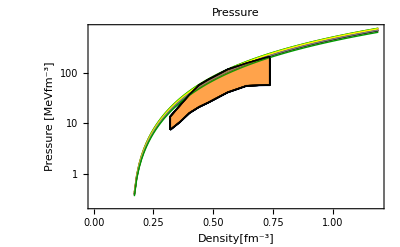

```mathematica
Show[PLsol1EoS[[2]],newPLsol2EoS,newPLsol3EoS2,newPLsol4EoS2,newPLsol5EoS2,newPLsol6EoS2,newPLsol7EoS2,newPLsol8EoS2,newPLsol9EoS2,newPLsol10EoS2,newPLsol11EoS2]
```

### Binding energy versus density

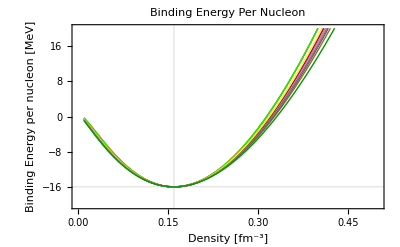

```mathematica
Show[PLsol1EoS[[5]],newPLsol2EoS5,newPLsol3EoS5,newPLsol4EoS5,newPLsol5EoS5,newPLsol6EoS5,newPLsol7EoS5,newPLsol8EoS5,newPLsol9EoS5,newPLsol10EoS5,newPLsol11EoS5]
```

## Total time to run notebook

Time in seconds

```mathematica
TotalTimeForNB=AbsoluteTime[]-StartTime
```

16845.77701

Time in minutes

```mathematica
TotalTimeForNB/60
```

280.7629501

Time in hours

```mathematica
TotalTimeForNB/3600
```

4.679382502

## Extra - Inclusion of Fock term correction to the scalar field

For these cases the term DϵσFDσ must be uncommented in FSigma and that cell re-run. Then the below cells re-run. WARNING: Do not use with the option Effρs, this will lead to a recursive error and many warnings.

### 12. "MyQMC700Numδσ" - (m^*)_σ changes with total baryonic density

```mathematica
sol12 =SatProperties["Effρv","Numerical",Gσ,Gω,Gρ,∞,∞,∞,0]//AbsoluteTiming
```

{9.35859,{0.16,-15.865,30.,11.31775456414725,7.24551973073528,4.518551832808334,11.93415147645819,10.67549411236348,8.357238178385703,22.7890964144231,789.56329211652,695.21097595547,340.4179724113179,53.27027307583741,147.7016,115.895155731237,16.5600028111129,18.3006343157676,0.,2.89041237147121,-4.05269258608195,-1.891912643507,0,0.}}

Extract data for tables below

```mathematica
MyQMC700NumδσOnlyCC=ExtractCCData[sol12[[2]],"MyQMC700δσNum"];
MyQMC700NumδσNMSat = ExtractNMSatData[sol12[[2]],"MyQMC700δσNum"];
MyQMC700NumδσFockEnDen = ExtractFockEnDen[sol12[[2]],"MyQMC700δσNum"];
```

### 13. "MyQMC700πNumδσ" - (m^*)_σ changes with total baryonic density

```mathematica
sol13 =SatProperties["Effρv","Numerical",Gσ,Gω,Gρ,∞,∞,∞,∞]//AbsoluteTiming
```

{18.2878,{0.16,-15.865,30.,10.62583848252372,7.085894329234268,3.918762772014398,11.56359879447587,10.55724376323773,7.782831574843669,22.3853333335,784.381348180079,705.672540942238,320.7682777128249,52.13812164266653,147.7016,117.503091277066,15.9784013629134,17.8974546669723,0.,2.82180576450303,-3.9634080757563,-1.64078162862873,-0.894963367069797,0.}}

Extract data for tables below

```mathematica
MyQMC700πNumδσOnlyCC=ExtractCCData[sol13[[2]],"MyQMC700πδσNum"];
MyQMC700πNumδσNMSat = ExtractNMSatData[sol13[[2]],"MyQMC700πδσNum"];
MyQMC700πNumδσFockEnDen = ExtractFockEnDen[sol13[[2]],"MyQMC700πδσNum"];
```

### Extra - Tables with Fock correction to the scalar field

```mathematica
MyDataδσCCOnly = {CCOnlyTableHeadings,CCOnlyTableUnits,MyQMC700NumδσOnlyCC,MyQMC700πNumδσOnlyCC};
```

```mathematica
Grid[MyDataδσCCOnly,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,LightGray,None}}]
```

Model | B. En.^* | S_0^* | ρ_0^* | G_σ | G_ω | G_ρ | g_σ | g_ω | g_ρ
 | [MeV] | [MeV] | [fm^-3] | [fm^-2] | [fm^-2] | [fm^-2] |   |   |  
MyQMC700δσNum | -15.865 | 30. | 0.16 | 11.318 | 7.2455 | 4.5186 | 11.934 | 10.675 | 8.3572
MyQMC700πδσNum | -15.865 | 30. | 0.16 | 10.626 | 7.0859 | 3.9188 | 11.564 | 10.557 | 7.7828

```mathematica
MyDataδσNMSat={NMSatTableHeadings,NMSatTableUnits,MyQMC700NumδσNMSat,MyQMC700πNumδσNMSat};
```

```mathematica
Grid[MyDataδσNMSat,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,LightGray,None}}]
```

Model | B. En.^* | S_0^* | ρ_0^* | σ_0 | (m^*)_σ | (M^*)_N | K_0 | L_0
 | [MeV] | [MeV] | [fm^-3] | [MeV] | [MeV] | [MeV] | [MeV] | [MeV]
MyQMC700δσNum | -15.865 | 30. | 0.16 | 22.789 | 789.56 | 695.21 | 340.42 | 53.27
MyQMC700πδσNum | -15.865 | 30. | 0.16 | 22.385 | 784.38 | 705.67 | 320.77 | 52.138

```mathematica
MyDataFockEnDen ={FockEnDenTableHeadings,FockEnDenTableUnits,MyQMC700NumδσFockEnDen,MyQMC700πNumδσFockEnDen};
```

```mathematica
Grid[MyDataFockEnDen,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,LightGray,None}}]
```

Model | B. En.^* | S_0^* | ρ_0^* | (SuperscriptBox[ϵ, F])_σ | (ϵ^F)_ω | (ϵ^F)_ρ | (ϵ^F)_π
 | [MeV] | [MeV] | [fm^-3] | [MeVfm^-3] | [MeVfm^-3] | [MeVfm^-3] | [MeVfm^-3]
MyQMC700δσNum | -15.865 | 30. | 0.16 | 2.8904 | -4.0527 | -1.8919 | 0
MyQMC700πδσNum | -15.865 | 30. | 0.16 | 2.8218 | -3.9634 | -1.6408 | -0.89496